```mathematica
Needs["NumericalDifferentialEquationAnalysis`"]
WriteDirectory="/Users/neerajsarna/sciebo/DG_moments_deal/Results_Discrete_Velocity/1D_Heat_Conduction";
```

## Core routines

### polynomials and Grads distribution

```mathematica
f0[c_]=1/(√(2π))Exp[-c^2/2];
H[i_,c_]=1/(√Gamma[i+1] 2^(i/2))HermiteH[i,c/√2];
fG[c_,n_]:=∑_(k=0)^(n-1) α[k]H[k,c]f0[c];

fM[θ_,v_,ρ_,c_]:=(c v-θ/2+(c^2 θ)/2+ρ)f0[c];

(*routines needed for wall density computation*)
Prod1[c_]=H[1,c]H[0,c]f0[c];
Prod2[c_]=H[1,c]H[2,c]f0[c];
```

### Moments computation

```mathematica
(*multiply from the right by the discrete distribution function for velocity.*)
Arrayv[gaussloc_,gaussW_]:=Table[gaussloc⟦ii⟧gaussW⟦ii⟧,{ii,1,Length[gaussW]}];

(*Compute the velocity corresponding to positive molecular velocities*)
ArrayvPlus[gaussloc_,gaussW_]:=Module[{positioncplus,result},

positioncplus=Flatten[Position[gaussloc,_?(#>0&)]];
result=Flatten[ConstantArray[0,{1,Length[gaussloc]}]];
result⟦positioncplus⟧=Table[gaussloc⟦positioncplus⟦ii⟧⟧gaussW⟦positioncplus⟦ii⟧⟧,{ii,1,Length[positioncplus]}];
result
];

(*Compute the velocity corresponding to negative molecular velocity*)
ArrayvNegative[gaussloc_,gaussW_]:=Module[{positioncplus,result},

positioncplus=Flatten[Position[gaussloc,_?(#<0&)]];
result=Flatten[ConstantArray[0,{1,Length[gaussloc]}]];
result⟦positioncplus⟧=Table[gaussloc⟦positioncplus⟦ii⟧⟧gaussW⟦positioncplus⟦ii⟧⟧,{ii,1,Length[positioncplus]}];
result
];


(*Compute the velocity corresponding to positive molecular velocities*)
ArrayρPlus[gaussloc_,gaussW_]:=Module[{positioncplus,result},

positioncplus=Flatten[Position[gaussloc,_?(#>0&)]];
result=Flatten[ConstantArray[0,{1,Length[gaussloc]}]];
result⟦positioncplus⟧=Table[gaussW⟦positioncplus⟦ii⟧⟧,{ii,1,Length[positioncplus]}];
result
];

(*Compute the velocity corresponding to negative molecular velocity*)
ArrayρNegative[gaussloc_,gaussW_]:=Module[{positioncplus,result},

positioncplus=Flatten[Position[gaussloc,_?(#<0&)]];
result=Flatten[ConstantArray[0,{1,Length[gaussloc]}]];
result⟦positioncplus⟧=Table[gaussW⟦positioncplus⟦ii⟧⟧,{ii,1,Length[positioncplus]}];
result
];

Arrayρ[gaussloc_,gaussW_]:=Table[gaussW⟦ii⟧,{ii,1,Length[gaussW]}];

(*positive outgoing velocity*)
ArrayρW[gaussloc_,gaussW_]:=Module[{positioncplus,result},

positioncplus=Flatten[Position[gaussloc,_?(#<0&)]];
result=Flatten[ConstantArray[0,{1,Length[gaussloc]}]];
result⟦positioncplus⟧=(*-1/IntegrateCplus[Prod1,gaussloc,gaussW]*)-√(2π)Table[gaussloc⟦positioncplus⟦ii⟧⟧gaussW⟦positioncplus⟦ii⟧⟧,{ii,1,Length[positioncplus]}];

result
];

(*negative outgoing velocity*)
ArrayρWMinus[gaussloc_,gaussW_]:=Module[{positioncplus,result},

positioncplus=Flatten[Position[gaussloc,_?(#>0&)]];
result=Flatten[ConstantArray[0,{1,Length[gaussloc]}]];

result⟦positioncplus⟧=(*-1/IntegrateCminus[Prod1,gaussloc,gaussW] *)√(2π)Table[gaussloc⟦positioncplus⟦ii⟧⟧gaussW⟦positioncplus⟦ii⟧⟧,{ii,1,Length[positioncplus]}];
result
];

Arrayθ[gaussloc_,gaussW_]:=Table[gaussW⟦ii⟧(gaussloc⟦ii⟧^2-1),{ii,1,Length[gaussW]}];

(*the following function returns an array which when dotted with the value of f at different velocity points gives back the value of the deviation of the Maxewellian from the global equilibrium*)
ConstructMaxwellian[jj_,gaussloc_,gaussW_]:=Module[{result,c},
c =gaussloc⟦jj⟧;
result = c f0[c]Arrayv[gaussloc,gaussW]-f0[c] Arrayθ[gaussloc,gaussW]/2+f0[c] c^2 Arrayθ[gaussloc,gaussW]/2+Arrayρ[gaussloc,gaussW]f0[c]]

Computeρ[solution_,locationc_,locationx_]:=Module[{result,pointsx,pointsc,function,data},
pointsc=Length[locationc];
pointsx=Length[solution]/pointsc;
result=Flatten[ConstantArray[0,{1,pointsx}]];
Do[
data=Table[{locationc⟦jj⟧,solution⟦pointsc*(ii-1)+jj⟧},{jj,1,Length[locationc]}];
function=Interpolation[data];
result⟦ii⟧={locationx⟦ii⟧,NIntegrate[function[x],{x,locationc⟦1⟧,locationc⟦-1⟧}]};,{ii,1,pointsx}];

result

]

Computeθ[solution_,locationc_]:=Module[{result,pointsx,pointsc,function,data},

pointsc=Length[locationc];
pointsx=Length[solution]/pointsc;
result=Flatten[ConstantArray[0,{1,pointsx}]];
Do[
data=Table[{locationc⟦jj⟧,solution⟦pointsc*(ii-1)+jj⟧},{jj,1,Length[locationc]}];
function=Interpolation[data];
result⟦ii⟧=NIntegrate[function[x](x^2-1),{x,locationc⟦1⟧,locationc⟦-1⟧}];,{ii,1,pointsx}];

result

]

Computef[solution_,locationc_]:=Module[{function,pointsc,pointsx,data},
pointsc=Length[locationc];
pointsx=Length[solution]/pointsc;
function=Flatten[ConstantArray[0,{1,pointsx}]];

Do[
data=Table[{locationc⟦jj⟧,solution⟦pointsc*(ii-1)+jj⟧},{jj,1,Length[locationc]}];
function⟦ii⟧=Interpolation[data];
,{ii,1,pointsx}];

function
]
```

### Quadrature computation

```mathematica
(*given a function, integrate on the positive velocity domain*)
IntegrateCplus[f_,gaussloc_,gaussW_]:=Module[{positionCplus,result},
positionCplus=Flatten[Position[gaussloc,_?(#>0&)]];

result=Sum[f[gaussloc⟦positionCplus⟦ii⟧⟧]gaussW⟦positionCplus⟦ii⟧⟧,{ii,1,Length[positionCplus]}];

result

]

IntegrateCminus[f_,gaussloc_,gaussW_]:=Module[{positionCplus,result},
positionCplus=Flatten[Position[gaussloc,_?(#<0&)]];

result=Sum[f[gaussloc⟦positionCplus⟦ii⟧⟧]gaussW⟦positionCplus⟦ii⟧⟧,{ii,1,Length[positionCplus]}];

result
]
```

### routines for projection onto discrete space

```mathematica
Projectf[locationc_,f_]:=Table[f[locationc⟦ii⟧],{ii,1,Length[locationc]}];
```

### Plot help

```mathematica
ExactError2[e1_,h1_,h2_,p_]:=Exp[Log[e1]-Log[(h1/h2)^p]];

Plotf[solution_,locationc_,locationx_,pointsc_]:=Module[{pointsx,data},
pointsx=Length[solution]/pointsc;

data=Flatten[Table[Table[{locationx⟦ii⟧,locationc⟦jj⟧,solution⟦pointsc*(ii-1)+jj⟧},{jj,1,pointsc}],{ii,1,pointsx}],1];

ListPlot3D[data,PlotRange->Full]
]
```

### Difference Operators

#### Difference Operators

```mathematica
DifferenceOperator[locationc_,δx_]:=Module[{pointsc,Cell,Right,Left,cNegR,cNegL,OperatorR,OperatorL,OperatorCell},

pointsc=Length[locationc];
(*the difference operators*)
OperatorCell=ConstantArray[0,{pointsc,pointsc}];
OperatorR=ConstantArray[0,{pointsc,pointsc}];
OperatorL=ConstantArray[0,{pointsc,pointsc}];

OperatorCell=DiagonalMatrix[Abs[locationc]];

(*negative values of the velocity for the right operator*)
cNegR=Select[locationc,#<0&];
cNegR=Join[cNegR,Flatten[ConstantArray[0,{1,Length[locationc]-Length[cNegR]}]]];

cNegL=Select[locationc,#>0&];
cNegL=Join[Flatten[ConstantArray[0,{1,Length[locationc]-Length[cNegL]}]],-cNegL];

OperatorR=DiagonalMatrix[cNegR];
OperatorL=DiagonalMatrix[cNegL];

{1/δx OperatorCell,1/δx OperatorR,1/δx OperatorL}
]

OperatorW[gaussloc_,gaussW_,δx_,θW0_,θW1_]:=Module[{cNeg,cPos,LeftW,RightW,cplus,cneg,pointsc,Leftrhs,Rightrhs,function1,function2,α},
pointsc=Length[gaussloc];

cNeg=Select[gaussloc,#<0&];
cNeg=Join[cNeg,Flatten[ConstantArray[0,{1,Length[gaussloc]-Length[cNeg]}]]];

cPos=Select[gaussloc,#>0&];
cPos=Join[Flatten[ConstantArray[0,{1,Length[gaussloc]-Length[cPos]}]],cPos];

LeftW=ConstantArray[0,{pointsc,pointsc}];
RightW=ConstantArray[0,{pointsc,pointsc}];
Leftrhs=Flatten[ConstantArray[0,{1,pointsc}]];
Rightrhs=Flatten[ConstantArray[0,{1,pointsc}]];

Print[Style["Wall at the left",FontColor->Red,FontSize->14]];
Print[Style["Wall at the right",FontColor->Red,FontSize->14]];

(*the following factor is introduced if we consider numerical integration*)
α=(*IntegrateCplus[Prod2,gaussloc,gaussW]/IntegrateCplus[Prod1,gaussloc,gaussW]*)1/(√2);

Do[
cplus=cPos⟦ii⟧;
cneg=cNeg⟦ii⟧;
LeftW⟦ii,All⟧=-cplus/δx f0[cplus]ArrayρW[gaussloc,gaussW];
RightW⟦ii,All⟧=cneg/δx f0[cneg]ArrayρWMinus[gaussloc,gaussW];

(*Routine for Wall*)
Leftrhs⟦ii⟧=cplus/δx( (θW0 H[2,cplus])/(√2)-(α θW0)/(√2))f0[cplus];
Rightrhs⟦ii⟧=-cneg/δx( (θW1 H[2,cneg])/(√2)-(α θW1)/(√2))f0[cneg];

(*Routine for the Maxwellian influx*)
(*Leftrhs⟦ii⟧=cplus/δx fM[θW0,0,0.1,cplus];
Rightrhs⟦ii⟧=-cneg/δx fM[θW1,0,0.2,cneg];*)


,{ii,1,Length[gaussloc]}];

{LeftW,RightW,Leftrhs,Rightrhs}

]
```

### Exact ρ for Kn ∞

```mathematica
(*computes the exact density for the half maxwellians for the exact solution of the heat conduction problem at Kn = ∞*)
ComputeρKn∞[ρ_,θ1_,θ2_]:=Module[{ρ1,ρ2,solution},

solution=Flatten[Solve[{ρ1+θ1/2==ρ2+θ2/2,ρ1+ρ2==2ρ},{ρ1,ρ2}]];

{ρ1,ρ2}/.solution
]
```

### Writting routine

```mathematica
Writef[spacex_,gaussloc_,gaussW_,f_,filename_]:=Module[{pointsc,pointsx,str,IDCell},

pointsx=Length[spacex];
pointsc=Length[gaussloc];

str = OpenWrite[StringJoin[WriteDirectory,"/",filename,"x",ToString[pointsx],"c",ToString[pointsc],".dat"]];
WriteString[str,"#x points: ",ToString[pointsx]," #c points: ",ToString[pointsc],"\n"];
WriteString[str,"xloc: ","cloc: ","weight: ","f","\n"];
WriteString[str,"values below 10e-5 have been chopped","\n"];
Do[IDCell=pointsc*(ii-1);
Do[WriteString[str,ToString[spacex⟦ii⟧]," ",ToString[gaussloc⟦jj⟧]," ",ToString[gaussW⟦jj⟧]," ",ToString[f⟦IDCell+jj⟧],"\n"],{jj,1,pointsc}];,{ii,1,pointsx}];

Close[str];
]
```

## Solver Routine

### Inhomogeneous solver

```mathematica
Clear[Solver]
```

```mathematica
(*nx = number of intervals between the wall and same for dc*)
```

```mathematica
Solver[nx_,nc_,Kn_,θW0_,θW1_]:=Module[{dx,dc,cl,cr,pointsx,pointsc,Matglobal,Matu1,Matu1u2,locationx,locationc,IDCell,IDNeighborL,Matu1uL,Matu1uR,IDNeighborR,MatProduction,c,ContriMaxwellian,Rhs,Rhslocal,hasL,hasR},

(*left end point of the velocity space*)
cl = -8;

(*right end point of the velocity space*)
cr = 8;

(*spacing in the physical space*)
dx = 1/nx;

(*spacing in the velocity space*)
dc = (cr-cl)/nc;

(*points in the interior*)
pointsx = nx-1;
pointsc=nc-1;
locationx=Range[0,1,dx]⟦2;;-2⟧;
locationc=Range[cl,cr,dc]⟦2;;-2⟧;

Matglobal=ConstantArray[0,{pointsx *pointsc,pointsx* pointsc}];
Rhs=Flatten[ConstantArray[0,{1,pointsx*pointsc}]];


(*contribution from the maxwellian*)
ContriMaxwellian=Table[locationc⟦ii⟧^2/2+locationc⟦ii⟧+1/2,{ii,1,pointsc}];

(*We precompute the contribution from the production term*)
MatProduction=ConstantArray[0,{pointsc,pointsc}];
Do[(*contribution from fm*)
MatProduction⟦ii,All⟧=1/Kn ConstructMaxwellian[ii,locationc,dc];

(*contribution from f*)
MatProduction⟦ii,ii⟧+=-1/Kn;,{ii,1,Length[locationc]}];


(*assemble the matrix for the interior nodes*)
Do[

(*location on the diagonal of the present block*)
   IDCell=pointsc*(ii-1)+1;


(*coupling with itself*)
Matu1=ConstantArray[0,{pointsc,pointsc}];

(*coupling with the neighbor*)
Matu1uL=ConstantArray[0,{pointsc,pointsc}];
Matu1uR=ConstantArray[0,{pointsc,pointsc}];
Rhslocal=Flatten[ConstantArray[0,{1,pointsc}]];


If[ii≠1 && ii≠pointsx,
Do[
c = locationc⟦jj⟧;
(*Upwinding routine*)
If[c>0,
Matu1⟦jj,jj⟧=c/dx;
Matu1uL⟦jj,jj⟧=-c/dx;

hasL=True;
IDNeighborL=pointsc*(ii-2)+1;,


Matu1⟦jj,jj⟧=-c/dx;
Matu1uR⟦jj,jj⟧=c/dx;
hasR=True;
IDNeighborR=pointsc*ii+1;];

,{jj,1,pointsc}];

(*handle the boundary points*)
,If[ii==1,
Do[
c = locationc⟦jj⟧;
If[c>0,
(*first all the contribution from ρW*)
Matu1⟦jj,All⟧=-c/dx f0[c]ArrayρW[locationc,dc];

(*contribution from the cell itself*)
Matu1⟦jj,jj⟧+=c/dx;

(*Inhomogeneity from the wall.*)
Rhslocal⟦jj⟧=c/dx( (θW0 H[2,c])/(√2)-θW0/2)f0[c];

(*(*source of f with an amplitude 1*)
(*contribution from the cell itself*)
Matu1⟦jj,jj⟧=c/dx;

(*Influx from the wall. A constant f with value 1. *)
Rhslocal⟦jj⟧=c/dx;*)

(*sink at x = 0*)
(*contribution from the cell itself*)
(*Matu1⟦jj,jj⟧=c/dx;*)
,
Matu1⟦jj,jj⟧=-c/dx;
Matu1uR⟦jj,jj⟧=c/dx;
hasR=True;
IDNeighborR=pointsc*ii+1;
];,{jj,1,pointsc}];,
Do[
c = locationc⟦jj⟧;
If[c>0,
Matu1⟦jj,jj⟧=c/dx;
Matu1uL⟦jj,jj⟧=-c/dx;
hasL=True;
IDNeighborL=pointsc*(ii-2)+1;,
(*first all the contribution from ρW*)
Matu1⟦jj,All⟧=c/dx f0[c]ArrayρWMinus[locationc,dc];

(*contribution from the cell itself*)
Matu1⟦jj,jj⟧+=-c/dx;

(*Inhomogeneity from the wall. θW1 is the temperature of the wall at x = 1*)
Rhslocal⟦jj⟧=-c/dx( (θW1 H[2,c])/(√2)-θW1/2)f0[c];

(*totally absorbing wall*)
(*Matu1⟦jj,jj⟧=-c/dx;*)
];,{jj,1,pointsc}];

];
];


 
   
Matglobal⟦IDCell;;IDCell+pointsc-1,IDCell;;IDCell+pointsc-1⟧+=Matu1;  
Matglobal⟦IDCell;;IDCell+pointsc-1,IDCell;;IDCell+pointsc-1⟧+=-MatProduction;  

(*only insert if the cell has a neighbor on the left*)
If[hasL,Matglobal⟦IDCell;;IDCell+pointsc-1,IDNeighborL;;IDNeighborL+pointsc-1⟧+=Matu1uL;];

(*only insert if the cell has a neighbor on the right*)
If[hasR,Matglobal⟦IDCell;;IDCell+pointsc-1,IDNeighborR;;IDNeighborR+pointsc-1⟧+=Matu1uR;];



Rhs⟦IDCell;;IDCell+pointsc-1⟧+=Rhslocal;

,{ii,1,pointsx}];


(*{Computeθ[Inverse[Matglobal].Rhs,locationc],
LinearSolve[Matglobal,Rhs],locationc,locationx,dx}*)
Matglobal
]
```

### Inhomogeneous solver(faster)

```mathematica
Clear[SolverFaster]
```

```mathematica
(*nx = number of intervals between the wall and same for dc*)
```

```mathematica
SolverFaster[nx_,nc_,Kn_,initialf_,θW0_,θW1_]:=Module[{dx,cl,cr,pointsx,pointsc,Matglobal,Matu1,Matu1u2,locationx,locationc,IDCell,IDNeighborL,Matu1uL,Matu1uR,IDNeighborR,MatProduction,c,ContriMaxwellian,Rhs,Rhslocal,hasL,hasR,OperatorCell,OperatorR,OperatorL,OperatorLeftW,OperatorRightW,RhsLeftW,RhsRightW,hasrhs,f0,θOld,θNew,δt,t,gaussloc,gaussW,gaussWx,ρOld,ρNew,ρWLeft,ρWRight,vWRight,vWLeft,RhsNew,assemblationtime,solvingtime,datacomputationtime,arrayθ,arrayρ,arrayv,MatglobalNew},

(*left end point of the velocity space*)
cl = -8;

(*right end point of the velocity space*)
cr = 8;

(*spacing in the physical space*)
dx = 1/nx;


gaussloc=Join[GaussianQuadratureWeights[nc,cl,0]⟦All,1⟧,GaussianQuadratureWeights[nc,0,cr]⟦All,1⟧];
gaussW=Join[GaussianQuadratureWeights[nc,cl,0]⟦All,2⟧,GaussianQuadratureWeights[nc,0,cr]⟦All,2⟧];

(*points in the interior*)
pointsx = nx-1;
pointsc=Length[gaussloc];
locationx=Range[0,1,dx]⟦2;;-2⟧;
locationc=gaussloc;


(*contribution from the maxwellian*)
ContriMaxwellian=Table[locationc⟦ii⟧^2/2+locationc⟦ii⟧+1/2,{ii,1,pointsc}];

(*We precompute the contribution from the production term*)
MatProduction=ConstantArray[0,{pointsc,pointsc}];

Do[(*contribution from fm*)
MatProduction⟦ii,All⟧=1/Kn ConstructMaxwellian[ii,gaussloc,gaussW];

(*contribution from f*)
MatProduction⟦ii,ii⟧+=-1/Kn;,{ii,1,Length[gaussloc]}];

{OperatorCell,OperatorR,OperatorL}=DifferenceOperator[locationc,dx];
{OperatorLeftW,OperatorRightW,RhsLeftW,RhsRightW}=OperatorW[gaussloc,gaussW,dx,θW0,θW1];

f0=Flatten[ConstantArray[0,{1,pointsc*pointsx}]];

Do[IDCell=pointsc*(ii-1)+1;f0⟦IDCell;;IDCell+pointsc-1⟧=Projectf[locationc,initialf];,{ii,1,pointsx}];

θOld=Flatten[ConstantArray[10,{1,pointsx}]];
θNew=Flatten[ConstantArray[100,{1,pointsx}]];
δt=1.0;
t = 0;


Matglobal=ConstantArray[0,{pointsx *pointsc,pointsx* pointsc}];
Rhs=Flatten[ConstantArray[0,{1,pointsx*pointsc}]];


Print["Performing assemblation"];
(*assemble the matrix for the interior nodes*)
(*we first assemble the matrix which is independent of the solution*)
assemblationtime=AbsoluteTiming[
Do[

(*coupling with itself*)
Matu1=ConstantArray[0,{pointsc,pointsc}];

(*coupling with the neighbor*)
Matu1uL=ConstantArray[0,{pointsc,pointsc}];
Matu1uR=ConstantArray[0,{pointsc,pointsc}];

(**)
Rhslocal=Flatten[ConstantArray[0,{1,pointsc}]];

(*location on the diagonal of the present block*)
   IDCell=pointsc*(ii-1)+1;

If[ii≠ 1 && ii≠ pointsx,
Matu1=OperatorCell;
Matu1uR=OperatorR;
Matu1uL=OperatorL;

hasR=True;
hasL=True;
hasrhs=False;

IDNeighborL=pointsc*(ii-2)+1;
IDNeighborR=pointsc*ii+1;
];

If[ii == 1,
(*Wall*)
Matu1=OperatorCell+OperatorLeftW;
hasrhs=True;
Rhslocal=RhsLeftW;

(*Maxwellian Influx*)
(*Matu1=OperatorCell;
hasrhs = True;
Rhslocal=RhsLeftW;*)

Matu1uR=OperatorR;
hasR=True;
IDNeighborR=pointsc*ii+1;
];

If[ii==pointsx,
(*wall from a maxwellian influx*)
Matu1=OperatorCell+OperatorRightW;
hasrhs=True;
Rhslocal=RhsRightW;

(*No Reflection wall*)
(*Matu1=OperatorCell;
hasrhs=False;*)

(*Maxwellian influx*)
(*Matu1=OperatorCell;
hasrhs = True;
Rhslocal=RhsRightW;*)


Matu1uL=OperatorL;
hasL=True;
IDNeighborL=pointsc*(ii-2)+1;
];


 
   
Matglobal⟦IDCell;;IDCell+pointsc-1,IDCell;;IDCell+pointsc-1⟧+=Matu1;  
Matglobal⟦IDCell;;IDCell+pointsc-1,IDCell;;IDCell+pointsc-1⟧+=-MatProduction;  

(*only insert if the cell has a neighbor on the left*)
If[hasL,Matglobal⟦IDCell;;IDCell+pointsc-1,IDNeighborL;;IDNeighborL+pointsc-1⟧+=Matu1uL;];

(*only insert if the cell has a neighbor on the right*)
If[hasR,Matglobal⟦IDCell;;IDCell+pointsc-1,IDNeighborR;;IDNeighborR+pointsc-1⟧+=Matu1uR;];

If[hasrhs,Rhs⟦IDCell;;IDCell+pointsc-1⟧+=Rhslocal];

,{ii,1,pointsx}]]⟦1⟧;

(*time stepping*)
MatglobalNew=SparseArray[δt Matglobal+IdentityMatrix[pointsc * pointsx]];


(*arrays for moment computations*)
arrayθ=Arrayθ[gaussloc,gaussW];
arrayv=Arrayv[gaussloc,gaussW];
arrayρ=Arrayρ[gaussloc,gaussW];

(*Time stepping for unsteady problems*)
Print["Time Stepping"];
While[Norm[θOld-θNew]>10^-9,

RhsNew=Flatten[ConstantArray[0,{1,pointsc*pointsx}]];
RhsNew=δt Rhs+f0;
(*ρOld=Sum[arrayρ.f0⟦pointsc*(ii-1)+1;;pointsc*ii⟧,{ii,1,pointsx}];*)
θOld=Sum[arrayθ.f0⟦pointsc*(ii-1)+1;;pointsc*ii⟧,{ii,1,pointsx}];

t+=δt;
solvingtime=AbsoluteTiming[
f0= LinearSolve[MatglobalNew,RhsNew,Method->"Krylov"]]⟦1⟧;

θNew=Sum[arrayθ.f0⟦pointsc*(ii-1)+1;;pointsc*ii⟧,{ii,1,pointsx}];
(*Print["Temperature deviation: ",Abs[θNew-θOld]];*)
(*ρNew=Sum[arrayρ.f0⟦pointsc*(ii-1)+1;;pointsc*ii⟧,{ii,1,pointsx}];*)

];


ρWLeft=ArrayρW[gaussloc,gaussW].(f0⟦1;;pointsc⟧)-θW0/2;
ρWRight=ArrayρWMinus[gaussloc,gaussW].(f0⟦-pointsc;;-1⟧)-θW1/2;
vWLeft=ArrayvNegative[gaussloc,gaussW].f0⟦1;;pointsc⟧+Integrate[c fM[θW0,0,ρWLeft,c],{c,0,∞}];
vWRight=ArrayvPlus[gaussloc,gaussW].f0⟦-pointsc;;-1⟧+Integrate[c fM[θW1,0,ρWRight,c],{c,-∞,0}];

Print["Velocity at left wall and right wall: ",Abs[vWLeft]," ",Abs[vWRight]];
Print["Residum: ",Norm[Matglobal.f0-Rhs]];
{Computeθ[f0,locationc],f0,gaussloc,gaussW,locationx}
]
```

### Homogeneous solver

```mathematica
HomogeneousSolver[Kn_,initialf_,nc_,δt_]:=Module[{f0,pointsc,locationc,cl,cr,dc,t,fm,deviation,ρOld,ρNew,gaussloc,gaussW,MatProd,ρMax,count,vMax,vNew,θMax,θNew},
(*left end point of the velocity space*)
cl = -8;

(*right end point of the velocity space*)
cr = 8;

(*spacing in the velocity space*)
dc = (cr-cl)/nc;


gaussloc=Join[GaussianQuadratureWeights[nc,cl,0]⟦All,1⟧,GaussianQuadratureWeights[nc,0,cr]⟦All,1⟧];

gaussW=Join[GaussianQuadratureWeights[nc,cl,0]⟦All,2⟧,GaussianQuadratureWeights[nc,0,cr]⟦All,2⟧];
pointsc=Length[gaussloc];

f0=Projectf[gaussloc,initialf];
(*construct the Maxwellian*)


t = 0;



MatProd=ConstantArray[0,{pointsc,pointsc}];
MatProd=Table[ConstructMaxwellian[ii,gaussloc,gaussW],{ii,1,Length[gaussloc]}];
fm=MatProd.f0;

ρOld=Arrayρ[gaussloc,gaussW].f0;
ρMax=Arrayρ[gaussloc,gaussW].fm;
Print["Difference in density: ",Abs[ρMax-ρOld]];

deviation=Norm[f0-MatProd.f0];
count = 0;
While[deviation>10^-5,

ρOld=Arrayρ[gaussloc,gaussW].f0;

(*simple forward euler step*)
f0 = f0+δt/Kn(fm-f0);
t=t+δt;

(*construct the Maxwellian*)
fm=MatProd.f0;
ρMax=Arrayρ[gaussloc,gaussW].fm;
ρNew=Arrayρ[gaussloc,gaussW].f0;

vMax=Arrayv[gaussloc,gaussW].fm;
vNew = Arrayv[gaussloc,gaussW].f0;

θMax=Arrayv[gaussloc,gaussW].fm;
θNew = Arrayv[gaussloc,gaussW].f0;


deviation=Norm[fm-f0];
count++;

If[Mod[count,10]==0,Print["Density deviation: ",Abs[ρOld-ρNew]];
If[Abs[ρNew-ρMax]<10^-5&& Abs[vNew-vMax]<10^-5 && Abs[θNew-θMax]<10^-5,Print[Style["Conserved",FontColor->Green]],Print[Style["Not Conserved",FontColor->Red]]];Print["Deviation from Equilibrium: ",deviation];
Print["Time: ",t];];


];

Print[Style["Stopped iterating at: ",FontColor->Red],deviation];
{f0,gaussloc,gaussW}

]
```

## Results

### Exponential decay to zero

```mathematica
Kn=10.0;
min=9;
max=50;
Do[
points = n-1;
vpoint=n-2;
result=Solver[n,n,Kn,1.0];
rho=result⟦1⟧;
exactf[x_,c_]:=Piecewise[{{Exp[-x/(Kn c)],c≥0},{0,c≤0}}];
error[n]={result⟦5⟧,Max[Table[Abs[result⟦2⟧⟦points*(ii-1)+1+vpoint⟧-exactf[result⟦4⟧⟦ii⟧,result⟦3⟧⟦vpoint+1⟧]],{ii,1,Length[result⟦4⟧]}]]};,{n,min,max}]
```

Part::partw: Part 5 of Solver[9, 9, 10., 1.] does not exist.

Part::partw: Part 5 of Solver[10, 10, 10., 1.] does not exist.

Part::partw: Part 5 of Solver[11, 11, 10., 1.] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

{{0.02,1/50000},{0.1,0.0001}}

Part::partw: Part 5 of Solver[9., 9., 10., 1.] does not exist.

Part::partw: Part 5 of Solver[10., 10., 10., 1.] does not exist.

Part::partw: Part 5 of Solver[11., 11., 10., 1.] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

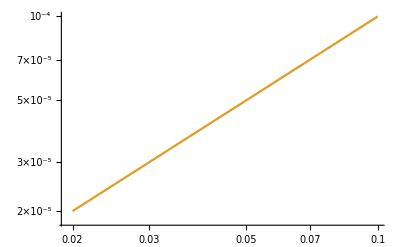

```mathematica
exactOrder={{0.02,2 10^-5},{0.1,ExactError2[2 10^-5,0.02,0.1,1]}}
ListLogLogPlot[{Table[error[ii],{ii,min,max}],exactOrder},Joined->True]
```

```mathematica
exactSolution[x]
```

exactSolution[x]

### Check Construct Maxwellian

#### convergence of Maxwellian

```mathematica
θ1=1.0;
ρ1=1.0;

θ2=2.0;
ρ2=3.0;
trialfm[c_]:=If[c<0,fM[θ1,0,ρ1,c],fM[θ2,0,ρ2,c]];

min=5;
max = 100;

Do[trialpointsc=ii;
trialcl=-8;
trialcr=8;

trialgaussloc=Join[GaussianQuadratureWeights[trialpointsc,trialcl,0]⟦All,1⟧,GaussianQuadratureWeights[trialpointsc,0,trialcr]⟦All,1⟧];

trialgaussW=Join[GaussianQuadratureWeights[trialpointsc,trialcl,0]⟦All,2⟧,GaussianQuadratureWeights[trialpointsc,0,trialcr]⟦All,2⟧];

Projecttrialfm=Projectf[trialgaussloc,trialfm];

(*maxwellian obtained by computing moments numerically*)
Numericalfm=Table[ConstructMaxwellian[ii,trialgaussloc,trialgaussW],{ii,1,Length[trialgaussloc]}].Projecttrialfm;

error[ii]={ii,Max[Abs[Projecttrialfm-Numericalfm]]};
errorρ[ii]={ii,Abs[Arrayρ[trialgaussloc,trialgaussW].Projecttrialfm-Arrayρ[trialgaussloc,trialgaussW].Numericalfm]};
,{ii,min,max,20}]
```

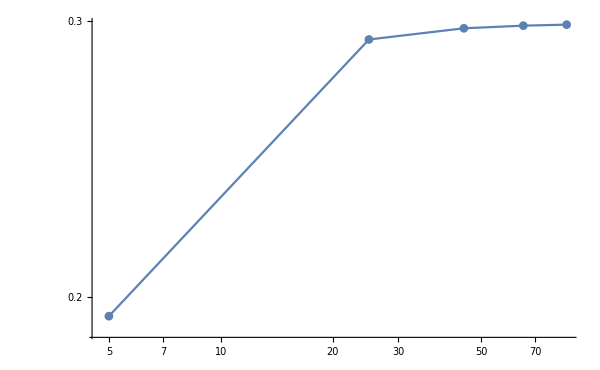

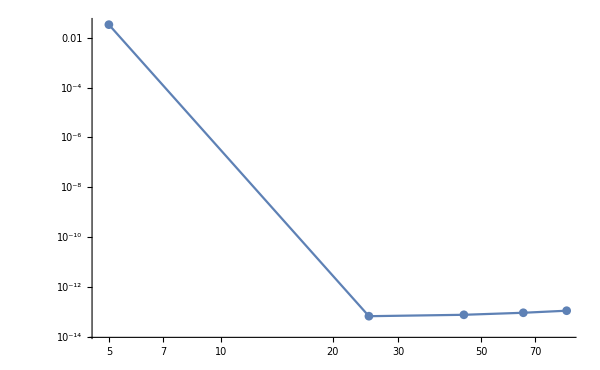

```mathematica
exactOrder={{0.5,5 10^-13},{0.1,ExactError2[5 10^-13,0.5,0.01,1]}};
ListLogLogPlot[{Table[error[ii],{ii,min,max,20}]},Joined->True,PlotRange->Full,ImageSize->600,PlotMarkers->Automatic]
ListLogLogPlot[{Table[errorρ[ii],{ii,min,max,20}]},Joined->True,PlotRange->Full,ImageSize->600,PlotMarkers->Automatic]
```

### Check ρW

```mathematica
trialv=0.01;
trialρ=0.01;
trialθ=1.0;
trialfm[c_]:=(1+c trialv-trialθ/2+(c^2 trialθ)/2+trialρ)f0[c];
trueρW=√(2π)Integrate[c trialfm[c],{c,-∞,0}];
min=30;
max = 800;

Do[trialpointsc=ii;
trialcl=-8;
trialcr=8;
trialdc = (trialcr-trialcl)/trialpointsc;
triallocationc=Range[trialcl,trialcr,trialdc]⟦2;;-2⟧;
Projecttrialfm=Projectf[triallocationc,trialfm];
NumericalρW=ArrayρW[triallocationc].Projecttrialfm;

error[ii]={trialdc,Abs[trueρW-NumericalρW]};
,{ii,min,max,20}]
```

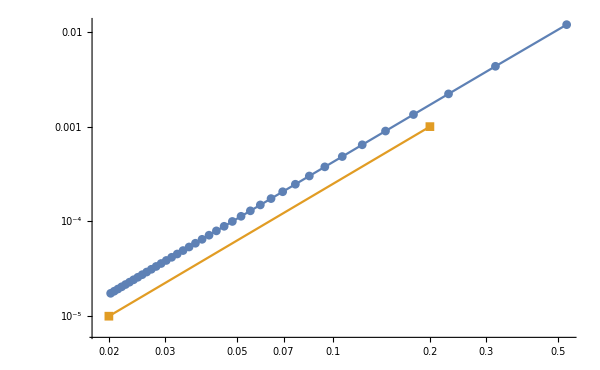

```mathematica
exactOrder={{0.2,10^-3},{0.02,ExactError2[10^-3,0.2,0.02,2]}};
ListLogLogPlot[{Table[error[ii],{ii,min,max,20}],exactOrder},Joined->True,PlotRange->Full,ImageSize->600,PlotMarkers->Automatic]
```

### Check ρWminus

```mathematica
trialv=0.01;
trialρ=0.01;
trialθ=1.0;
trialfm[c_]:=(1+c trialv-trialθ/2+(c^2 trialθ)/2+trialρ)f0[c];
trueρW=-√(2π)Integrate[c trialfm[c],{c,0,∞}];
min=30;
max = 800;

Do[trialpointsc=ii;
trialcl=-8;
trialcr=8;
trialdc = (trialcr-trialcl)/trialpointsc;
triallocationc=Range[trialcl,trialcr,trialdc]⟦2;;-2⟧;
Projecttrialfm=Projectf[triallocationc,trialfm];
NumericalρW=ArrayρWMinus[triallocationc,trialdc].Projecttrialfm;

error[ii]={trialdc,Abs[trueρW-NumericalρW]};
,{ii,min,max,20}]
```

Part::partd: Part specification 8/15 ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification 8/15 ⟦ 2 ⟧ is longer than depth of object.

Part::partd: Part specification 8/15 ⟦ 3 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

```mathematica
exactOrder={{0.2,10^-3},{0.02,ExactError2[10^-3,0.2,0.02,2]}};
ListLogLogPlot[{Table[error[ii],{ii,min,max,20}],exactOrder},Joined->True,PlotRange->Full,ImageSize->600,PlotMarkers->Automatic]
```

$Aborted

### Check Quadrature computation

```mathematica
Clear[exactPlus]
```

```mathematica
trialf1[c_]=H[1,c]H[0,c]f0[c];
exactPlus=Integrate[trialf1[c],{c,0,∞}];
exactMinus=Integrate[trialf1[c],{c,-∞,0}];

Do[quadX=Join[GaussianQuadratureWeights[ii,-10,0],GaussianQuadratureWeights[ii,0,10]]⟦All,1⟧;
quadW=Join[GaussianQuadratureWeights[ii,-10,0],GaussianQuadratureWeights[ii,0,10]]⟦All,2⟧;
errorPlus[ii]=Abs[IntegrateCplus[trialf1,quadX,quadW]-exactPlus];
errorMinus[ii]=Abs[IntegrateCminus[trialf1,quadX,quadW]-exactMinus];
,{ii,2,100,5}];
```

```mathematica
exactPlus
```

1/(2 √π)

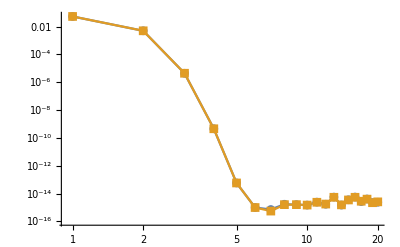

```mathematica
ListLogLogPlot[{Table[errorPlus[ii],{ii,2,100,5}],Table[errorMinus[ii],{ii,2,100,5}]},Joined->True,PlotMarkers->Automatic,PlotRange->Full]
```

### Check boundary operators

#### left wall

```mathematica
trialpoints=10;
trialgaussloc=Join[GaussianQuadratureWeights[trialpoints,-10,0]⟦All,1⟧,GaussianQuadratureWeights[trialpoints,0,10]⟦All,1⟧];
trialgaussW=Join[GaussianQuadratureWeights[trialpoints,-10,0]⟦All,2⟧,GaussianQuadratureWeights[trialpoints,0,10]⟦All,2⟧];
trialArrayρW=ArrayρW[trialgaussloc,trialgaussW];

trialLeftW=OperatorW[trialgaussloc,trialgaussW,dx,1.0,1.0]⟦1⟧;
```

Wall at the left

Wall at the right

```mathematica
(*trialArrayρW//MatrixForm*)
trialLeftW//MatrixForm
```

(0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.425499/dx | -0.901209/dx | -1.18961/dx | -1.2479/dx | -1.09774/dx | -0.813241/dx | -0.493282/dx | -0.22709/dx | -0.0652022/dx | -0.00562475/dx | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-1.76745/dx | -3.74348/dx | -4.94144/dx | -5.18359/dx | -4.55982/dx | -3.37807/dx | -2.04901/dx | -0.943295/dx | -0.270839/dx | -0.0233643/dx | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-1.45903/dx | -3.09023/dx | -4.07914/dx | -4.27903/dx | -3.76411/dx | -2.78858/dx | -1.69145/dx | -0.778687/dx | -0.223577/dx | -0.0192871/dx | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.168467/dx | -0.356814/dx | -0.471/dx | -0.49408/dx | -0.434625/dx | -0.321985/dx | -0.195304/dx | -0.0899114/dx | -0.0258154/dx | -0.002227/dx | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.0016347/dx | -0.00346231/dx | -0.0045703/dx | -0.00479426/dx | -0.00421734/dx | -0.00312435/dx | -0.00189512/dx | -0.000872447/dx | -0.000250497/dx | -0.0000216095/dx | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-(1.29108×10^-6)/dx | -(2.73451×10^-6)/dx | -(3.6096×10^-6)/dx | -(3.78648×10^-6)/dx | -(3.33083×10^-6)/dx | -(2.46759×10^-6)/dx | -(1.49675×10^-6)/dx | -(6.89053×10^-7)/dx | -(1.97841×10^-7)/dx | -(1.7067×10^-8)/dx | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-(1.65401×10^-10)/dx | -(3.50321×10^-10)/dx | -(4.62429×10^-10)/dx | -(4.8509×10^-10)/dx | -(4.26716×10^-10)/dx | -(3.16126×10^-10)/dx | -(1.9175×10^-10)/dx | -(8.82753×10^-11)/dx | -(2.53456×10^-11)/dx | -(2.18647×10^-12)/dx | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-(1.3492×10^-14)/dx | -(2.85762×10^-14)/dx | -(3.7721×10^-14)/dx | -(3.95695×10^-14)/dx | -(3.48079×10^-14)/dx | -(2.57869×10^-14)/dx | -(1.56414×10^-14)/dx | -(7.20075×10^-15)/dx | -(2.06748×10^-15)/dx | -(1.78354×10^-16)/dx | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-(4.01143×10^-18)/dx | -(8.49623×10^-18)/dx | -(1.12151×10^-17)/dx | -(1.17647×10^-17)/dx | -(1.0349×10^-17)/dx | -(7.6669×10^-18)/dx | -(4.65046×10^-18)/dx | -(2.14091×10^-18)/dx | -(6.14699×10^-19)/dx | -(5.30279×10^-20)/dx | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-(2.28866×10^-20)/dx | -(4.8474×10^-20)/dx | -(6.39864×10^-20)/dx | -(6.71219×10^-20)/dx | -(5.90447×10^-20)/dx | -(4.37424×10^-20)/dx | -(2.65325×10^-20)/dx | -(1.22147×10^-20)/dx | -(3.50708×10^-21)/dx | -(3.02543×10^-22)/dx | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.)

(0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.42561/dx | -0.901445/dx | -1.18992/dx | -1.24823/dx | -1.09802/dx | -0.813453/dx | -0.493411/dx | -0.227149/dx | -0.0652192/dx | -0.00562622/dx | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-1.76791/dx | -3.74445/dx | -4.94273/dx | -5.18494/dx | -4.56101/dx | -3.37895/dx | -2.04955/dx | -0.943541/dx | -0.27091/dx | -0.0233704/dx | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-1.45941/dx | -3.09103/dx | -4.08021/dx | -4.28015/dx | -3.7651/dx | -2.78931/dx | -1.69189/dx | -0.77889/dx | -0.223635/dx | -0.0192922/dx | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.168511/dx | -0.356907/dx | -0.471123/dx | -0.494209/dx | -0.434738/dx | -0.322069/dx | -0.195355/dx | -0.0899349/dx | -0.0258221/dx | -0.00222758/dx | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.00163513/dx | -0.00346322/dx | -0.0045715/dx | -0.00479551/dx | -0.00421844/dx | -0.00312517/dx | -0.00189561/dx | -0.000872674/dx | -0.000250562/dx | -0.0000216151/dx | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-(1.29141×10^-6)/dx | -(2.73523×10^-6)/dx | -(3.61054×10^-6)/dx | -(3.78747×10^-6)/dx | -(3.3317×10^-6)/dx | -(2.46824×10^-6)/dx | -(1.49714×10^-6)/dx | -(6.89233×10^-7)/dx | -(1.97893×10^-7)/dx | -(1.70715×10^-8)/dx | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-(1.65445×10^-10)/dx | -(3.50413×10^-10)/dx | -(4.6255×10^-10)/dx | -(4.85216×10^-10)/dx | -(4.26827×10^-10)/dx | -(3.16208×10^-10)/dx | -(1.918×10^-10)/dx | -(8.82983×10^-11)/dx | -(2.53522×10^-11)/dx | -(2.18704×10^-12)/dx | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-(1.34956×10^-14)/dx | -(2.85837×10^-14)/dx | -(3.77309×10^-14)/dx | -(3.95798×10^-14)/dx | -(3.4817×10^-14)/dx | -(2.57936×10^-14)/dx | -(1.56454×10^-14)/dx | -(7.20263×10^-15)/dx | -(2.06802×10^-15)/dx | -(1.78401×10^-16)/dx | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-(4.01247×10^-18)/dx | -(8.49845×10^-18)/dx | -(1.12181×10^-17)/dx | -(1.17678×10^-17)/dx | -(1.03517×10^-17)/dx | -(7.6689×10^-18)/dx | -(4.65167×10^-18)/dx | -(2.14147×10^-18)/dx | -(6.1486×10^-19)/dx | -(5.30417×10^-20)/dx | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-(2.28926×10^-20)/dx | -(4.84867×10^-20)/dx | -(6.40031×10^-20)/dx | -(6.71394×10^-20)/dx | -(5.90601×10^-20)/dx | -(4.37538×10^-20)/dx | -(2.65394×10^-20)/dx | -(1.22178×10^-20)/dx | -(3.50799×10^-21)/dx | -(3.02622×10^-22)/dx | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.)

### x = 0 wall and infinite sink at x = 1 (check for the boundary implementation at x = 0,Unsteady)

```mathematica
Clear[result2,trialf,spacec,spacex]
```

```mathematica
nx=25;
Kn=∞;
θW0=5.0;
θW1=3.0;
exactθ=0.5;
min=25;
max=55;
diff=5;

initialv=0.0;
initialρ=0.1;
initialθ=θW0;
initialf[c_]:=(c initialv-initialθ/2+(c^2 initialθ)/2+initialρ)f0[c];

Do[
Print[Style["Grid Points: ",FontColor->Green],ii];
result2[ii]=SolverFaster[nx,ii,Kn,initialf,θW0,θW1];
spacex[ii]=result2[ii]⟦5⟧;
spacec[ii]=result2[ii]⟦3⟧;
weights[ii]=result2[ii]⟦4⟧;
,{ii,min,max,diff}];
(*errorθ[25]={1/nx,Max[Abs[result2⟦1⟧-exactθ]]};*)
```

Grid Points: 25

Maxwellian influx on the left

Performing assemblation

Time Stepping

Time: 1.

Deviation in temperature: 7.74244

Performing assemblation

Time Stepping

Time: 2.

Deviation in temperature: 1.63336

Performing assemblation

Time Stepping

Time: 3.

Deviation in temperature: 0.274424

Performing assemblation

Time Stepping

Time: 4.

Deviation in temperature: 0.0387839

Performing assemblation

Time Stepping

Time: 5.

Deviation in temperature: 0.00500807

Performing assemblation

Time Stepping

Time: 6.

Deviation in temperature: 0.00061965

Performing assemblation

Time Stepping

Time: 7.

Deviation in temperature: 0.0000744441

Performing assemblation

Time Stepping

Time: 8.

Deviation in temperature: 8.62621×10^-6

Grid Points: 30

Maxwellian influx on the left

Performing assemblation

Time Stepping

Time: 1.

Deviation in temperature: 9.19859

Performing assemblation

Time Stepping

Time: 2.

Deviation in temperature: 2.45735

Performing assemblation

Time Stepping

Time: 3.

Deviation in temperature: 0.710316

Performing assemblation

Time Stepping

Time: 4.

Deviation in temperature: 0.239034

Performing assemblation

Time Stepping

Time: 5.

Deviation in temperature: 0.0857265

Performing assemblation

Time Stepping

Time: 6.

Deviation in temperature: 0.0294039

Performing assemblation

Time Stepping

Time: 7.

Deviation in temperature: 0.00925227

Performing assemblation

Time Stepping

Time: 8.

Deviation in temperature: 0.00265804

Performing assemblation

Time Stepping

Time: 9.

Deviation in temperature: 0.000701873

Performing assemblation

Time Stepping

Time: 10.

Deviation in temperature: 0.000171867

Performing assemblation

Time Stepping

Time: 11.

Deviation in temperature: 0.0000393547

Performing assemblation

Time Stepping

Time: 12.

Deviation in temperature: 8.48866×10^-6

Grid Points: 35

Maxwellian influx on the left

Performing assemblation

Time Stepping

Time: 1.

Deviation in temperature: 8.28199

Performing assemblation

Time Stepping

Time: 2.

Deviation in temperature: 1.83217

Performing assemblation

Time Stepping

Time: 3.

Deviation in temperature: 0.324139

Performing assemblation

Time Stepping

Time: 4.

Deviation in temperature: 0.0475068

Performing assemblation

Time Stepping

Time: 5.

Deviation in temperature: 0.00620372

Performing assemblation

Time Stepping

Time: 6.

Deviation in temperature: 0.000767682

Performing assemblation

Time Stepping

Time: 7.

Deviation in temperature: 0.000094661

Performing assemblation

Time Stepping

Time: 8.

Deviation in temperature: 0.0000119747

Performing assemblation

Time Stepping

Time: 9.

Deviation in temperature: 1.55534×10^-6

Grid Points: 40

Maxwellian influx on the left

Performing assemblation

Time Stepping

Time: 1.

Deviation in temperature: 8.99697

Performing assemblation

Time Stepping

Time: 2.

Deviation in temperature: 2.38795

Performing assemblation

Time Stepping

Time: 3.

Deviation in temperature: 0.764358

Performing assemblation

Time Stepping

Time: 4.

Deviation in temperature: 0.328548

Performing assemblation

Time Stepping

Time: 5.

Deviation in temperature: 0.155794

Performing assemblation

Time Stepping

Time: 6.

Deviation in temperature: 0.0698404

Performing assemblation

Time Stepping

Time: 7.

Deviation in temperature: 0.0284629

Performing assemblation

Time Stepping

Time: 8.

Deviation in temperature: 0.010558

Performing assemblation

Time Stepping

Time: 9.

Deviation in temperature: 0.00359844

Performing assemblation

Time Stepping

Time: 10.

Deviation in temperature: 0.0011379

Performing assemblation

Time Stepping

Time: 11.

Deviation in temperature: 0.000336713

Performing assemblation

Time Stepping

Time: 12.

Deviation in temperature: 0.0000939107

Performing assemblation

Time Stepping

Time: 13.

Deviation in temperature: 0.0000248382

Performing assemblation

Time Stepping

Time: 14.

Deviation in temperature: 6.2622×10^-6

Grid Points: 45

Maxwellian influx on the left

Performing assemblation

Time Stepping

Time: 1.

Deviation in temperature: 8.49369

Performing assemblation

Time Stepping

Time: 2.

Deviation in temperature: 1.97808

Performing assemblation

Time Stepping

Time: 3.

Deviation in temperature: 0.405617

Performing assemblation

Time Stepping

Time: 4.

Deviation in temperature: 0.0813239

Performing assemblation

Time Stepping

Time: 5.

Deviation in temperature: 0.0174221

Performing assemblation

Time Stepping

Time: 6.

Deviation in temperature: 0.00391607

Performing assemblation

Time Stepping

Time: 7.

Deviation in temperature: 0.00087045

Performing assemblation

Time Stepping

Time: 8.

Deviation in temperature: 0.000183914

Performing assemblation

Time Stepping

Time: 9.

Deviation in temperature: 0.000036398

Performing assemblation

Time Stepping

Time: 10.

Deviation in temperature: 6.73722×10^-6

Grid Points: 50

Maxwellian influx on the left

Performing assemblation

Time Stepping

Time: 1.

Deviation in temperature: 8.91002

Performing assemblation

Time Stepping

Time: 2.

Deviation in temperature: 2.31791

Performing assemblation

Time Stepping

Time: 3.

Deviation in temperature: 0.749823

Performing assemblation

Time Stepping

Time: 4.

Deviation in temperature: 0.360742

Performing assemblation

Time Stepping

Time: 5.

Deviation in temperature: 0.202166

Performing assemblation

Time Stepping

Time: 6.

Deviation in temperature: 0.108593

Performing assemblation

Time Stepping

Time: 7.

Deviation in temperature: 0.0532885

Performing assemblation

Time Stepping

Time: 8.

Deviation in temperature: 0.0238732

Performing assemblation

Time Stepping

Time: 9.

Deviation in temperature: 0.00984805

Performing assemblation

Time Stepping

Time: 10.

Deviation in temperature: 0.00377504

Performing assemblation

Time Stepping

Time: 11.

Deviation in temperature: 0.00135563

Performing assemblation

Time Stepping

Time: 12.

Deviation in temperature: 0.000459213

Performing assemblation

Time Stepping

Time: 13.

Deviation in temperature: 0.000147605

Performing assemblation

Time Stepping

Time: 14.

Deviation in temperature: 0.0000452472

Performing assemblation

Time Stepping

Time: 15.

Deviation in temperature: 0.0000132852

Performing assemblation

Time Stepping

Time: 16.

Deviation in temperature: 3.75025×10^-6

Grid Points: 55

Maxwellian influx on the left

Performing assemblation

Time Stepping

Time: 1.

Deviation in temperature: 8.59559

Performing assemblation

Time Stepping

Time: 2.

Deviation in temperature: 2.06191

Performing assemblation

Time Stepping

Time: 3.

Deviation in temperature: 0.471222

Performing assemblation

Time Stepping

Time: 4.

Deviation in temperature: 0.119463

Performing assemblation

Time Stepping

Time: 5.

Deviation in temperature: 0.034681

Performing assemblation

Time Stepping

Time: 6.

Deviation in temperature: 0.0103527

Performing assemblation

Time Stepping

Time: 7.

Deviation in temperature: 0.00293189

Performing assemblation

Time Stepping

Time: 8.

Deviation in temperature: 0.000767289

Performing assemblation

Time Stepping

Time: 9.

Deviation in temperature: 0.000185314

Performing assemblation

Time Stepping

Time: 10.

Deviation in temperature: 0.0000415593

Performing assemblation

Time Stepping

Time: 11.

Deviation in temperature: 8.71913×10^-6

```mathematica
Clear[f,ρW]
```

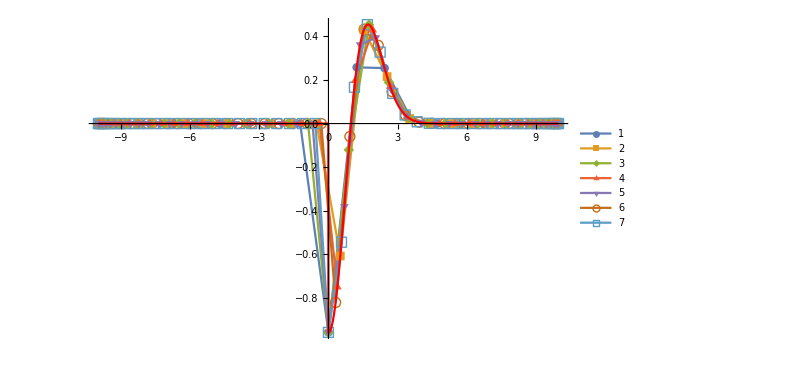

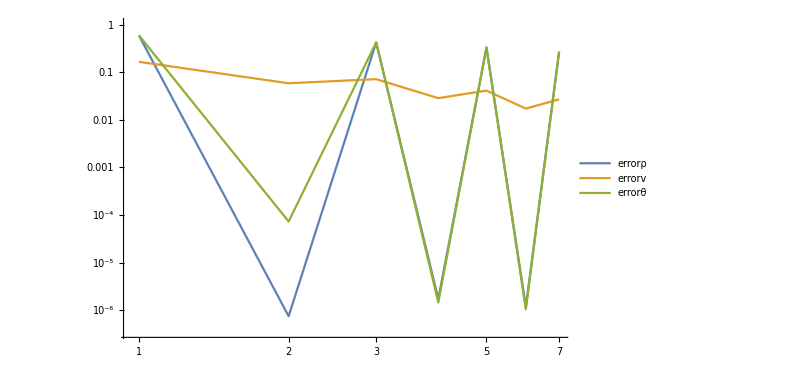

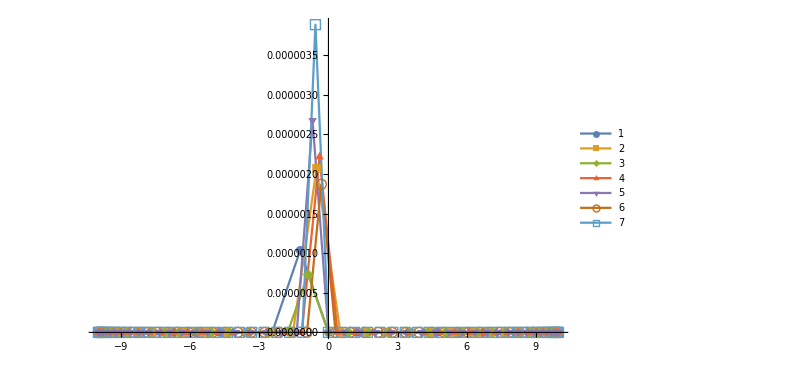

```mathematica
(*phase density function at the first space point but all of velocity points*)
f=Table[Table[{spacec[ii]⟦jj⟧,result2[ii]⟦2⟧⟦jj⟧},{jj,1,Length[spacec[ii]]}],{ii,min,max,diff}];

exactf[c_]:=If[c<0,0,fM[θW0,0,0.1,c]];
exactρ=NIntegrate[exactf[c],{c,-∞,∞}];
exactv=NIntegrate[exactf[c]c,{c,-∞,∞}];
exactθ=NIntegrate[(c^2-1)exactf[c],{c,-∞,∞}];


Numericalρ=Table[Arrayρ[spacec[ii],weights[ii]].result2[ii]⟦2⟧⟦1;;ii⟧,{ii,25,55,5}];
Numericalv=Table[Arrayv[spacec[ii],weights[ii]].result2[ii]⟦2⟧⟦1;;ii⟧,{ii,25,55,5}];
Numericalθ=Table[Arrayθ[spacec[ii],weights[ii]].result2[ii]⟦2⟧⟦1;;ii⟧,{ii,25,55,5}];

errorρ=Abs[Numericalρ-exactρ];
errorv=Abs[Numericalv-exactv];
errorθ=Abs[Numericalθ-exactθ];
errorf=Table[Table[{spacec[ii]⟦jj⟧,Abs[(exactf[x]/.{x->spacec[ii]⟦jj⟧})-f⟦ii/5-4⟧⟦All,2⟧⟦jj⟧]},{jj,1,Length[spacec[ii]]}],{ii,25,55,5}];



Show[{ListPlot[f,PlotRange->Full,Joined->True,PlotMarkers->Automatic,PlotLegends->Automatic],Plot[exactf[x],{x,-10,10},PlotLegends->"Exact Solution",PlotRange->Full]},ImageSize->600]

ListLogLogPlot[{errorρ,errorv,errorθ},Joined->True,ImageSize->600,PlotLegends->{"errorρ","errorv","errorθ"}]

ListPlot[errorf,Joined->True,PlotLegends->Automatic,PlotRange->Full,ImageSize->600,PlotMarkers->Automatic]
```

### Maxwellian influx from both the sides

```mathematica
Clear[result2,trialf,spacec,spacex]
```

```mathematica
nx=25;
Kn=∞;
θW0Ref=5.0;
θW1Ref=3.0;
exactθ=0.5;
min=10;
max=25;
diff=5;

initialv=0.0;
initialρ=0.1;
initialθ=θW0Ref;
initialf[c_]:=(c initialv-initialθ/2+(c^2 initialθ)/2+initialρ)f0[c];

Do[
Print[Style["Grid Points: ",FontColor->Green],ii];
result2[ii]=SolverFaster[nx,ii,Kn,initialf,θW0Ref,θW1Ref];
spacex[ii]=result2[ii]⟦5⟧;
spacec[ii]=result2[ii]⟦3⟧;
weights[ii]=result2[ii]⟦4⟧;
,{ii,min,max,diff}];
(*errorθ[25]={1/nx,Max[Abs[result2⟦1⟧-exactθ]]};*)
```

Grid Points: 10

Maxwellian influx

Maxwellian influx

Performing assemblation

Time Stepping

Time: 1.

Deviation in temperature: 3.48104

Deviation in density: 2.16683

Performing assemblation

Time Stepping

Time: 2.

Deviation in temperature: 0.884532

Deviation in density: 0.420444

Performing assemblation

Time Stepping

Time: 3.

Deviation in temperature: 0.299638

Deviation in density: 0.700121

Performing assemblation

Time Stepping

Time: 4.

Deviation in temperature: 0.190991

Deviation in density: 0.55111

Performing assemblation

Time Stepping

Time: 5.

Deviation in temperature: 0.160264

Deviation in density: 0.425613

Performing assemblation

Time Stepping

Time: 6.

Deviation in temperature: 0.140432

Deviation in density: 0.340981

Performing assemblation

Time Stepping

Time: 7.

Deviation in temperature: 0.120538

Deviation in density: 0.271654

Performing assemblation

Time Stepping

Time: 8.

Deviation in temperature: 0.0991498

Deviation in density: 0.208821

Performing assemblation

Time Stepping

Time: 9.

Deviation in temperature: 0.0775521

Deviation in density: 0.153227

Performing assemblation

Time Stepping

Time: 10.

Deviation in temperature: 0.0575884

Deviation in density: 0.107154

Performing assemblation

Time Stepping

Time: 11.

Deviation in temperature: 0.0406509

Deviation in density: 0.0715355

Performing assemblation

Time Stepping

Time: 12.

Deviation in temperature: 0.0273468

Deviation in density: 0.0457121

Performing assemblation

Time Stepping

Time: 13.

Deviation in temperature: 0.0175856

Deviation in density: 0.0280404

Performing assemblation

Time Stepping

Time: 14.

Deviation in temperature: 0.0108434

Deviation in density: 0.0165576

Performing assemblation

Time Stepping

Time: 15.

Deviation in temperature: 0.00643042

Deviation in density: 0.00943666

Performing assemblation

Time Stepping

Time: 16.

Deviation in temperature: 0.00367786

Deviation in density: 0.00520366

Performing assemblation

Time Stepping

Time: 17.

Deviation in temperature: 0.00203403

Deviation in density: 0.00278257

Performing assemblation

Time Stepping

Time: 18.

Deviation in temperature: 0.00109032

Deviation in density: 0.00144585

Performing assemblation

Time Stepping

Time: 19.

Deviation in temperature: 0.000567699

Deviation in density: 0.000731401

Performing assemblation

Time Stepping

Time: 20.

Deviation in temperature: 0.000287674

Deviation in density: 0.000360818

Performing assemblation

Time Stepping

Time: 21.

Deviation in temperature: 0.000142126

Deviation in density: 0.00017386

Performing assemblation

Time Stepping

Time: 22.

Deviation in temperature: 0.0000685702

Deviation in density: 0.0000819433

Performing assemblation

Time Stepping

Time: 23.

Deviation in temperature: 0.0000323539

Deviation in density: 0.0000378265

Performing assemblation

Time Stepping

Time: 24.

Deviation in temperature: 0.0000149496

Deviation in density: 0.0000171226

Performing assemblation

Time Stepping

Time: 25.

Deviation in temperature: 6.77293×10^-6

Deviation in density: 7.60876×10^-6

Grid Points: 15

Maxwellian influx

Maxwellian influx

Performing assemblation

Time Stepping

Time: 1.

Deviation in temperature: 3.53068

Deviation in density: 2.15467

Performing assemblation

Time Stepping

Time: 2.

Deviation in temperature: 0.949216

Deviation in density: 0.462578

Performing assemblation

Time Stepping

Time: 3.

Deviation in temperature: 0.327317

Deviation in density: 0.73674

Performing assemblation

Time Stepping

Time: 4.

Deviation in temperature: 0.162412

Deviation in density: 0.524702

Performing assemblation

Time Stepping

Time: 5.

Deviation in temperature: 0.09113

Deviation in density: 0.329539

Performing assemblation

Time Stepping

Time: 6.

Deviation in temperature: 0.0492504

Deviation in density: 0.211086

Performing assemblation

Time Stepping

Time: 7.

Deviation in temperature: 0.025131

Deviation in density: 0.148557

Performing assemblation

Time Stepping

Time: 8.

Deviation in temperature: 0.0128636

Deviation in density: 0.117877

Performing assemblation

Time Stepping

Time: 9.

Deviation in temperature: 0.0075535

Deviation in density: 0.10282

Performing assemblation

Time Stepping

Time: 10.

Deviation in temperature: 0.00556747

Deviation in density: 0.0942712

Performing assemblation

Time Stepping

Time: 11.

Deviation in temperature: 0.00479008

Deviation in density: 0.0877547

Performing assemblation

Time Stepping

Time: 12.

Deviation in temperature: 0.00438056

Deviation in density: 0.0813608

Performing assemblation

Time Stepping

Time: 13.

Deviation in temperature: 0.00407057

Deviation in density: 0.0744508

Performing assemblation

Time Stepping

Time: 14.

Deviation in temperature: 0.00376968

Deviation in density: 0.0669706

Performing assemblation

Time Stepping

Time: 15.

Deviation in temperature: 0.00344778

Deviation in density: 0.0591171

Performing assemblation

Time Stepping

Time: 16.

Deviation in temperature: 0.00310062

Deviation in density: 0.0511766

Performing assemblation

Time Stepping

Time: 17.

Deviation in temperature: 0.00273599

Deviation in density: 0.0434414

Performing assemblation

Time Stepping

Time: 18.

Deviation in temperature: 0.00236664

Deviation in density: 0.0361651

Performing assemblation

Time Stepping

Time: 19.

Deviation in temperature: 0.00200628

Deviation in density: 0.0295383

Performing assemblation

Time Stepping

Time: 20.

Deviation in temperature: 0.00166705

Deviation in density: 0.0236811

Performing assemblation

Time Stepping

Time: 21.

Deviation in temperature: 0.00135823

Deviation in density: 0.0186458

Performing assemblation

Time Stepping

Time: 22.

Deviation in temperature: 0.00108566

Deviation in density: 0.0144274

Performing assemblation

Time Stepping

Time: 23.

Deviation in temperature: 0.000851899

Deviation in density: 0.0109772

Performing assemblation

Time Stepping

Time: 24.

Deviation in temperature: 0.000656671

Deviation in density: 0.00821807

Performing assemblation

Time Stepping

Time: 25.

Deviation in temperature: 0.000497598

Deviation in density: 0.00605757

Performing assemblation

Time Stepping

Time: 26.

Deviation in temperature: 0.000370925

Deviation in density: 0.00439892

Performing assemblation

Time Stepping

Time: 27.

Deviation in temperature: 0.000272188

Deviation in density: 0.00314903

Performing assemblation

Time Stepping

Time: 28.

Deviation in temperature: 0.000196752

Deviation in density: 0.00222353

Performing assemblation

Time Stepping

Time: 29.

Deviation in temperature: 0.000140191

Deviation in density: 0.00154949

Performing assemblation

Time Stepping

Time: 30.

Deviation in temperature: 0.0000985231

Deviation in density: 0.00106622

Performing assemblation

Time Stepping

Time: 31.

Deviation in temperature: 0.0000683331

Deviation in density: 0.000724833

Performing assemblation

Time Stepping

Time: 32.

Deviation in temperature: 0.0000467998

Deviation in density: 0.000487055

Performing assemblation

Time Stepping

Time: 33.

Deviation in temperature: 0.000031667

Deviation in density: 0.000323643

Performing assemblation

Time Stepping

Time: 34.

Deviation in temperature: 0.0000211806

Deviation in density: 0.000212763

Performing assemblation

Time Stepping

Time: 35.

Deviation in temperature: 0.0000140103

Deviation in density: 0.000138436

Performing assemblation

Time Stepping

Time: 36.

Deviation in temperature: 9.16916×10^-6

Deviation in density: 0.0000891864

Grid Points: 20

Maxwellian influx

Maxwellian influx

Performing assemblation

Time Stepping

Time: 1.

Deviation in temperature: 3.47319

Deviation in density: 2.15578

Performing assemblation

Time Stepping

Time: 2.

Deviation in temperature: 0.898991

Deviation in density: 0.459496

Performing assemblation

Time Stepping

Time: 3.

Deviation in temperature: 0.280711

Deviation in density: 0.739192

Performing assemblation

Time Stepping

Time: 4.

Deviation in temperature: 0.133317

Deviation in density: 0.541338

Performing assemblation

Time Stepping

Time: 5.

Deviation in temperature: 0.082341

Deviation in density: 0.356966

Performing assemblation

Time Stepping

Time: 6.

Deviation in temperature: 0.0548995

Deviation in density: 0.236028

Performing assemblation

Time Stepping

Time: 7.

Deviation in temperature: 0.0368712

Deviation in density: 0.158907

Performing assemblation

Time Stepping

Time: 8.

Deviation in temperature: 0.024369

Deviation in density: 0.109082

Performing assemblation

Time Stepping

Time: 9.

Deviation in temperature: 0.0158662

Deviation in density: 0.0772172

Performing assemblation

Time Stepping

Time: 10.

Deviation in temperature: 0.0104918

Deviation in density: 0.0575493

Performing assemblation

Time Stepping

Time: 11.

Deviation in temperature: 0.00748548

Deviation in density: 0.0459747

Performing assemblation

Time Stepping

Time: 12.

Deviation in temperature: 0.00603672

Deviation in density: 0.0394781

Performing assemblation

Time Stepping

Time: 13.

Deviation in temperature: 0.0053983

Deviation in density: 0.0359546

Performing assemblation

Time Stepping

Time: 14.

Deviation in temperature: 0.00509653

Deviation in density: 0.0340416

Performing assemblation

Time Stepping

Time: 15.

Deviation in temperature: 0.00492135

Deviation in density: 0.0329195

Performing assemblation

Time Stepping

Time: 16.

Deviation in temperature: 0.00479595

Deviation in density: 0.0321248

Performing assemblation

Time Stepping

Time: 17.

Deviation in temperature: 0.00469175

Deviation in density: 0.0314079

Performing assemblation

Time Stepping

Time: 18.

Deviation in temperature: 0.00459548

Deviation in density: 0.0306394

Performing assemblation

Time Stepping

Time: 19.

Deviation in temperature: 0.00449893

Deviation in density: 0.0297552

Performing assemblation

Time Stepping

Time: 20.

Deviation in temperature: 0.00439601

Deviation in density: 0.0287269

Performing assemblation

Time Stepping

Time: 21.

Deviation in temperature: 0.00428187

Deviation in density: 0.0275466

Performing assemblation

Time Stepping

Time: 22.

Deviation in temperature: 0.00415275

Deviation in density: 0.0262197

Performing assemblation

Time Stepping

Time: 23.

Deviation in temperature: 0.00400601

Deviation in density: 0.0247609

Performing assemblation

Time Stepping

Time: 24.

Deviation in temperature: 0.00384028

Deviation in density: 0.0231919

Performing assemblation

Time Stepping

Time: 25.

Deviation in temperature: 0.00365547

Deviation in density: 0.0215392

Performing assemblation

Time Stepping

Time: 26.

Deviation in temperature: 0.0034528

Deviation in density: 0.0198322

Performing assemblation

Time Stepping

Time: 27.

Deviation in temperature: 0.00323461

Deviation in density: 0.0181016

Performing assemblation

Time Stepping

Time: 28.

Deviation in temperature: 0.00300422

Deviation in density: 0.0163776

Performing assemblation

Time Stepping

Time: 29.

Deviation in temperature: 0.00276556

Deviation in density: 0.0146884

Performing assemblation

Time Stepping

Time: 30.

Deviation in temperature: 0.00252294

Deviation in density: 0.013059

Performing assemblation

Time Stepping

Time: 31.

Deviation in temperature: 0.00228071

Deviation in density: 0.0115105

Performing assemblation

Time Stepping

Time: 32.

Deviation in temperature: 0.00204301

Deviation in density: 0.0100594

Performing assemblation

Time Stepping

Time: 33.

Deviation in temperature: 0.00181356

Deviation in density: 0.00871777

Performing assemblation

Time Stepping

Time: 34.

Deviation in temperature: 0.00159551

Deviation in density: 0.00749301

Performing assemblation

Time Stepping

Time: 35.

Deviation in temperature: 0.00139132

Deviation in density: 0.00638846

Performing assemblation

Time Stepping

Time: 36.

Deviation in temperature: 0.00120277

Deviation in density: 0.0054038

Performing assemblation

Time Stepping

Time: 37.

Deviation in temperature: 0.00103098

Deviation in density: 0.0045357

Performing assemblation

Time Stepping

Time: 38.

Deviation in temperature: 0.000876413

Deviation in density: 0.00377842

Performing assemblation

Time Stepping

Time: 39.

Deviation in temperature: 0.000739003

Deviation in density: 0.00312447

Performing assemblation

Time Stepping

Time: 40.

Deviation in temperature: 0.000618233

Deviation in density: 0.00256521

Performing assemblation

Time Stepping

Time: 41.

Deviation in temperature: 0.000513236

Deviation in density: 0.00209138

Performing assemblation

Time Stepping

Time: 42.

Deviation in temperature: 0.000422894

Deviation in density: 0.00169349

Performing assemblation

Time Stepping

Time: 43.

Deviation in temperature: 0.000345928

Deviation in density: 0.00136224

Performing assemblation

Time Stepping

Time: 44.

Deviation in temperature: 0.000280975

Deviation in density: 0.00108872

Performing assemblation

Time Stepping

Time: 45.

Deviation in temperature: 0.000226655

Deviation in density: 0.000864677

Performing assemblation

Time Stepping

Time: 46.

Deviation in temperature: 0.00018162

Deviation in density: 0.000682551

Performing assemblation

Time Stepping

Time: 47.

Deviation in temperature: 0.000144592

Deviation in density: 0.00053559

Performing assemblation

Time Stepping

Time: 48.

Deviation in temperature: 0.00011439

Deviation in density: 0.000417846

Performing assemblation

Time Stepping

Time: 49.

Deviation in temperature: 0.0000899446

Deviation in density: 0.000324156

Performing assemblation

Time Stepping

Time: 50.

Deviation in temperature: 0.0000703039

Deviation in density: 0.000250098

Performing assemblation

Time Stepping

Time: 51.

Deviation in temperature: 0.0000546355

Deviation in density: 0.000191934

Performing assemblation

Time Stepping

Time: 52.

Deviation in temperature: 0.0000422214

Deviation in density: 0.000146533

Performing assemblation

Time Stepping

Time: 53.

Deviation in temperature: 0.0000324504

Deviation in density: 0.000111308

Performing assemblation

Time Stepping

Time: 54.

Deviation in temperature: 0.0000248087

Deviation in density: 0.0000841353

Performing assemblation

Time Stepping

Time: 55.

Deviation in temperature: 0.000018869

Deviation in density: 0.000063292

Performing assemblation

Time Stepping

Time: 56.

Deviation in temperature: 0.0000142795

Deviation in density: 0.0000473905

Performing assemblation

Time Stepping

Time: 57.

Deviation in temperature: 0.0000107537

Deviation in density: 0.0000353231

Performing assemblation

Time Stepping

Time: 58.

Deviation in temperature: 8.06012×10^-6

Deviation in density: 0.0000262121

Grid Points: 25

Maxwellian influx

Maxwellian influx

Performing assemblation

Time Stepping

Time: 1.

Deviation in temperature: 3.45302

Deviation in density: 2.15568

Performing assemblation

Time Stepping

Time: 2.

Deviation in temperature: 0.887002

Deviation in density: 0.459295

Performing assemblation

Time Stepping

Time: 3.

Deviation in temperature: 0.274285

Deviation in density: 0.737191

Performing assemblation

Time Stepping

Time: 4.

Deviation in temperature: 0.129914

Deviation in density: 0.537368

Performing assemblation

Time Stepping

Time: 5.

Deviation in temperature: 0.0799108

Deviation in density: 0.354229

Performing assemblation

Time Stepping

Time: 6.

Deviation in temperature: 0.0535132

Deviation in density: 0.238821

Performing assemblation

Time Stepping

Time: 7.

Deviation in temperature: 0.0374346

Deviation in density: 0.168891

Performing assemblation

Time Stepping

Time: 8.

Deviation in temperature: 0.0271518

Deviation in density: 0.124166

Performing assemblation

Time Stepping

Time: 9.

Deviation in temperature: 0.0201599

Deviation in density: 0.0932165

Performing assemblation

Time Stepping

Time: 10.

Deviation in temperature: 0.0150665

Deviation in density: 0.0704745

Performing assemblation

Time Stepping

Time: 11.

Deviation in temperature: 0.0111931

Deviation in density: 0.0533815

Performing assemblation

Time Stepping

Time: 12.

Deviation in temperature: 0.00824654

Deviation in density: 0.0406562

Performing assemblation

Time Stepping

Time: 13.

Deviation in temperature: 0.00609232

Deviation in density: 0.0314493

Performing assemblation

Time Stepping

Time: 14.

Deviation in temperature: 0.00462918

Deviation in density: 0.0250299

Performing assemblation

Time Stepping

Time: 15.

Deviation in temperature: 0.00373109

Deviation in density: 0.0207261

Performing assemblation

Time Stepping

Time: 16.

Deviation in temperature: 0.00323638

Deviation in density: 0.0179486

Performing assemblation

Time Stepping

Time: 17.

Deviation in temperature: 0.00298249

Deviation in density: 0.0162179

Performing assemblation

Time Stepping

Time: 18.

Deviation in temperature: 0.00285012

Deviation in density: 0.0151716

Performing assemblation

Time Stepping

Time: 19.

Deviation in temperature: 0.00277261

Deviation in density: 0.0145523

Performing assemblation

Time Stepping

Time: 20.

Deviation in temperature: 0.00271906

Deviation in density: 0.0141873

Performing assemblation

Time Stepping

Time: 21.

Deviation in temperature: 0.00267654

Deviation in density: 0.0139654

Performing assemblation

Time Stepping

Time: 22.

Deviation in temperature: 0.00263979

Deviation in density: 0.0138176

Performing assemblation

Time Stepping

Time: 23.

Deviation in temperature: 0.00260652

Deviation in density: 0.0137022

Performing assemblation

Time Stepping

Time: 24.

Deviation in temperature: 0.00257556

Deviation in density: 0.013594

Performing assemblation

Time Stepping

Time: 25.

Deviation in temperature: 0.0025461

Deviation in density: 0.013478

Performing assemblation

Time Stepping

Time: 26.

Deviation in temperature: 0.0025175

Deviation in density: 0.0133447

Performing assemblation

Time Stepping

Time: 27.

Deviation in temperature: 0.00248914

Deviation in density: 0.0131879

Performing assemblation

Time Stepping

Time: 28.

Deviation in temperature: 0.0024604

Deviation in density: 0.0130035

Performing assemblation

Time Stepping

Time: 29.

Deviation in temperature: 0.00243064

Deviation in density: 0.0127886

Performing assemblation

Time Stepping

Time: 30.

Deviation in temperature: 0.00239916

Deviation in density: 0.0125413

Performing assemblation

Time Stepping

Time: 31.

Deviation in temperature: 0.00236528

Deviation in density: 0.0122606

Performing assemblation

Time Stepping

Time: 32.

Deviation in temperature: 0.00232832

Deviation in density: 0.0119463

Performing assemblation

Time Stepping

Time: 33.

Deviation in temperature: 0.00228762

Deviation in density: 0.0115991

Performing assemblation

Time Stepping

Time: 34.

Deviation in temperature: 0.0022426

Deviation in density: 0.0112203

Performing assemblation

Time Stepping

Time: 35.

Deviation in temperature: 0.00219281

Deviation in density: 0.010812

Performing assemblation

Time Stepping

Time: 36.

Deviation in temperature: 0.00213788

Deviation in density: 0.0103771

Performing assemblation

Time Stepping

Time: 37.

Deviation in temperature: 0.00207763

Deviation in density: 0.00991871

Performing assemblation

Time Stepping

Time: 38.

Deviation in temperature: 0.00201204

Deviation in density: 0.00944084

Performing assemblation

Time Stepping

Time: 39.

Deviation in temperature: 0.00194125

Deviation in density: 0.00894764

Performing assemblation

Time Stepping

Time: 40.

Deviation in temperature: 0.00186556

Deviation in density: 0.00844355

Performing assemblation

Time Stepping

Time: 41.

Deviation in temperature: 0.00178543

Deviation in density: 0.0079331

Performing assemblation

Time Stepping

Time: 42.

Deviation in temperature: 0.00170144

Deviation in density: 0.00742081

Performing assemblation

Time Stepping

Time: 43.

Deviation in temperature: 0.00161429

Deviation in density: 0.00691108

Performing assemblation

Time Stepping

Time: 44.

Deviation in temperature: 0.00152476

Deviation in density: 0.00640807

Performing assemblation

Time Stepping

Time: 45.

Deviation in temperature: 0.00143365

Deviation in density: 0.00591561

Performing assemblation

Time Stepping

Time: 46.

Deviation in temperature: 0.00134182

Deviation in density: 0.00543717

Performing assemblation

Time Stepping

Time: 47.

Deviation in temperature: 0.0012501

Deviation in density: 0.00497576

Performing assemblation

Time Stepping

Time: 48.

Deviation in temperature: 0.0011593

Deviation in density: 0.00453394

Performing assemblation

Time Stepping

Time: 49.

Deviation in temperature: 0.00107015

Deviation in density: 0.00411377

Performing assemblation

Time Stepping

Time: 50.

Deviation in temperature: 0.000983356

Deviation in density: 0.00371683

Performing assemblation

Time Stepping

Time: 51.

Deviation in temperature: 0.00089951

Deviation in density: 0.00334423

Performing assemblation

Time Stepping

Time: 52.

Deviation in temperature: 0.000819124

Deviation in density: 0.00299664

Performing assemblation

Time Stepping

Time: 53.

Deviation in temperature: 0.000742617

Deviation in density: 0.00267431

Performing assemblation

Time Stepping

Time: 54.

Deviation in temperature: 0.000670311

Deviation in density: 0.00237715

Performing assemblation

Time Stepping

Time: 55.

Deviation in temperature: 0.000602438

Deviation in density: 0.00210472

Performing assemblation

Time Stepping

Time: 56.

Deviation in temperature: 0.000539138

Deviation in density: 0.00185632

Performing assemblation

Time Stepping

Time: 57.

Deviation in temperature: 0.000480475

Deviation in density: 0.00163103

Performing assemblation

Time Stepping

Time: 58.

Deviation in temperature: 0.000426438

Deviation in density: 0.00142773

Performing assemblation

Time Stepping

Time: 59.

Deviation in temperature: 0.000376951

Deviation in density: 0.00124519

Performing assemblation

Time Stepping

Time: 60.

Deviation in temperature: 0.000331889

Deviation in density: 0.00108208

Performing assemblation

Time Stepping

Time: 61.

Deviation in temperature: 0.000291078

Deviation in density: 0.000937018

Performing assemblation

Time Stepping

Time: 62.

Deviation in temperature: 0.000254312

Deviation in density: 0.000808583

Performing assemblation

Time Stepping

Time: 63.

Deviation in temperature: 0.00022136

Deviation in density: 0.000695377

Performing assemblation

Time Stepping

Time: 64.

Deviation in temperature: 0.000191972

Deviation in density: 0.00059602

Performing assemblation

Time Stepping

Time: 65.

Deviation in temperature: 0.000165887

Deviation in density: 0.000509185

Performing assemblation

Time Stepping

Time: 66.

Deviation in temperature: 0.000142842

Deviation in density: 0.000433601

Performing assemblation

Time Stepping

Time: 67.

Deviation in temperature: 0.000122574

Deviation in density: 0.000368071

Performing assemblation

Time Stepping

Time: 68.

Deviation in temperature: 0.000104827

Deviation in density: 0.000311476

Performing assemblation

Time Stepping

Time: 69.

Deviation in temperature: 0.0000893523

Deviation in density: 0.000262783

Performing assemblation

Time Stepping

Time: 70.

Deviation in temperature: 0.0000759149

Deviation in density: 0.000221041

Performing assemblation

Time Stepping

Time: 71.

Deviation in temperature: 0.0000642933

Deviation in density: 0.000185386

Performing assemblation

Time Stepping

Time: 72.

Deviation in temperature: 0.0000542812

Deviation in density: 0.000155037

Performing assemblation

Time Stepping

Time: 73.

Deviation in temperature: 0.0000456884

Deviation in density: 0.000129291

Performing assemblation

Time Stepping

Time: 74.

Deviation in temperature: 0.0000383408

Deviation in density: 0.000107523

Performing assemblation

Time Stepping

Time: 75.

Deviation in temperature: 0.0000320806

Deviation in density: 0.0000891775

Performing assemblation

Time Stepping

Time: 76.

Deviation in temperature: 0.0000267655

Deviation in density: 0.0000737657

Performing assemblation

Time Stepping

Time: 77.

Deviation in temperature: 0.0000222681

Deviation in density: 0.0000608583

Performing assemblation

Time Stepping

Time: 78.

Deviation in temperature: 0.0000184754

Deviation in density: 0.000050081

Performing assemblation

Time Stepping

Time: 79.

Deviation in temperature: 0.0000152871

Deviation in density: 0.0000411087

Performing assemblation

Time Stepping

Time: 80.

Deviation in temperature: 0.0000126155

Deviation in density: 0.0000336607

Performing assemblation

Time Stepping

Time: 81.

Deviation in temperature: 0.0000103838

Deviation in density: 0.0000274955

Performing assemblation

Time Stepping

Time: 82.

Deviation in temperature: 8.52507×10^-6

Deviation in density: 0.0000224062

```mathematica
Clear[f,ρW]
```

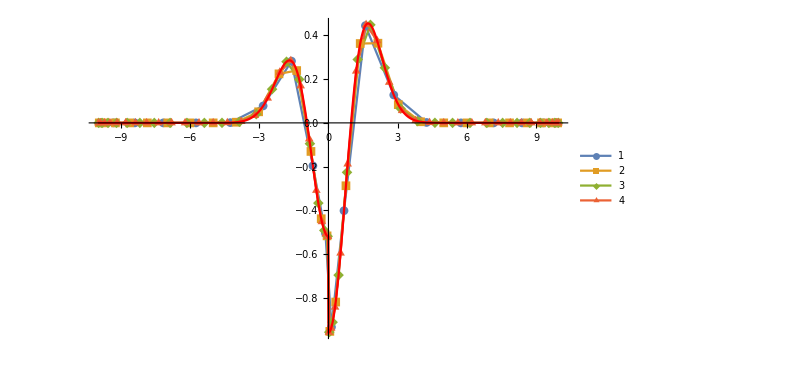

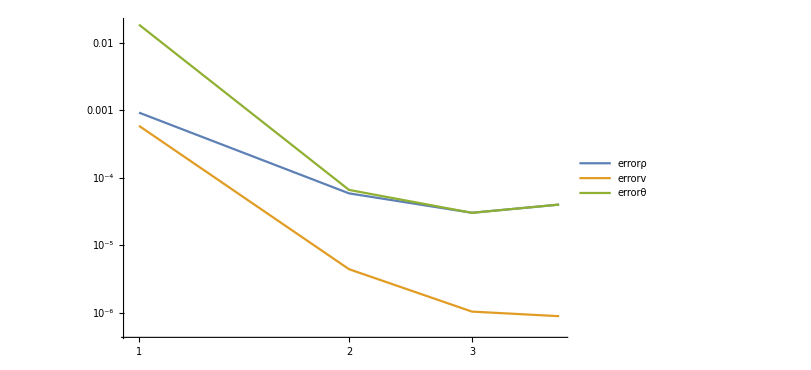

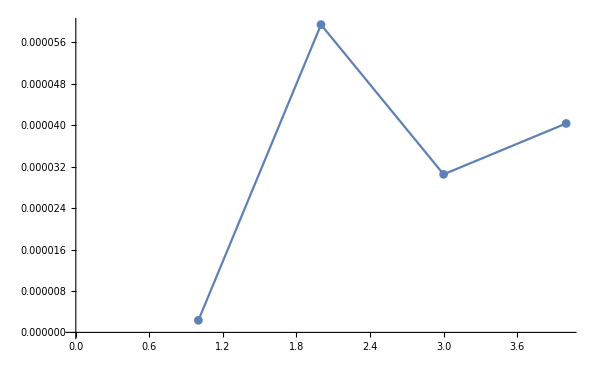

```mathematica
(*phase density function at the first space point but all of velocity points*)
f=Table[Table[{spacec[ii]⟦jj⟧,result2[ii]⟦2⟧⟦jj⟧},{jj,1,Length[spacec[ii]]}],{ii,min,max,diff}];

exactf[c_]:=If[c<0,fM[θW1Ref,0,0.2,c],fM[θW0Ref,0,0.1,c]];
exactρ=NIntegrate[exactf[c],{c,-∞,∞}];
exactv=NIntegrate[exactf[c]c,{c,-∞,∞}];
exactθ=NIntegrate[(c^2-1)exactf[c],{c,-∞,∞}];


Numericalρ=Table[Arrayρ[spacec[ii],weights[ii]].result2[ii]⟦2⟧⟦1;;2 ii⟧,{ii,min,max,diff}];
Numericalv=Table[Arrayv[spacec[ii],weights[ii]].result2[ii]⟦2⟧⟦1;;2ii⟧,{ii,min,max,diff}];
Numericalθ=Table[Arrayθ[spacec[ii],weights[ii]].result2[ii]⟦2⟧⟦1;;2ii⟧,{ii,min,max,diff}];

errorρ=Abs[Numericalρ-exactρ];
errorv=Abs[Numericalv-exactv];
errorθ=Abs[Numericalθ-exactθ];
errorf=Table[Table[{spacec[ii]⟦jj⟧,Abs[(exactf[x]/.{x->spacec[ii]⟦jj⟧})-f⟦ii/5-1⟧⟦All,2⟧⟦jj⟧]},{jj,1,Length[spacec[ii]]}],{ii,min,max,diff}];

L1errorf=Table[Arrayρ[spacec[ii],weights[ii]].errorf⟦ii/5-1⟧⟦All,2⟧,{ii,min,max,diff}];



Show[{ListPlot[f,PlotRange->Full,Joined->True,PlotMarkers->Automatic,PlotLegends->Automatic],Plot[exactf[x],{x,-10,10},PlotLegends->"Exact Solution",PlotRange->Full]},ImageSize->600]

ListLogLogPlot[{errorρ,errorv,errorθ},Joined->True,ImageSize->600,PlotLegends->{"errorρ","errorv","errorθ"}]

ListPlot[L1errorf,Joined->True,PlotLegends->Automatic,PlotRange->Full,ImageSize->600,PlotMarkers->Automatic]
```

```mathematica
L1
```

```mathematica
2
```

### Computing two maxwellians with Hermite basis (Low Jump)

```mathematica
Clear[f]
```

```mathematica
θW0=0.1;
θW1=0.3;
exactf[c_]:=If[c<0,fM[θW1,0,0.2,c],fM[θW0,0,0.1,c]];
valuesα=Table[α[ii]->NIntegrate[H[ii,c]exactf[c],{c,-∞,∞}],{ii,0,50}];
```

```mathematica
errorf=Table[NIntegrate[Abs[exactf[c]-(fG[c,ii]/.valuesα)],{c,-10,10}],{ii,5,25}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in c near {c} = {1.17156}. NIntegrate obtained 0.00667639 and 3.88953×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in c near {c} = {-1.79719}. NIntegrate obtained 0.00236219 and 4.13115×10^-8 for the integral and error estimates.

$Aborted

```mathematica
Do[f[ii][c_]=(fG[c,ii]/.valuesα);,{ii,5,15}];
plotf[c_]=Table[f[ii][c],{ii,5,15}];
```

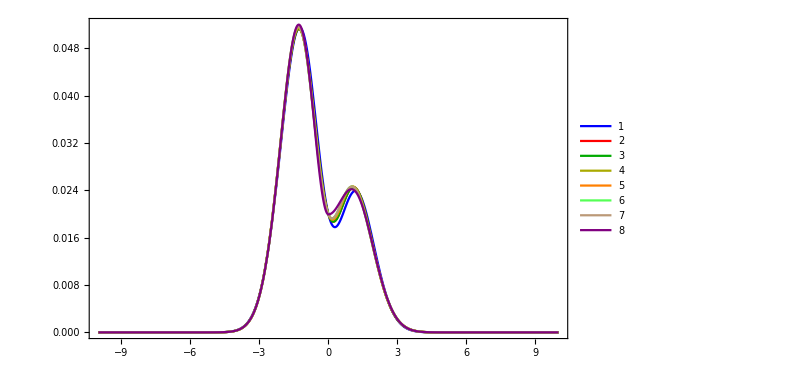

```mathematica
Plot[{f[5][c],f[6][c],f[7][c],f[8][c],f[9][c],f[10][c],f[11][c],exactf[c]},{c,-10,10},PlotRange->Full,PlotStyle->colorlist⟦1;;8⟧,PlotLegends->Automatic]
```

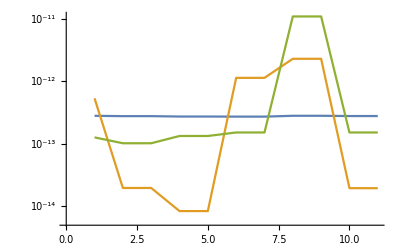

```mathematica
exactρ=Integrate[exactf[c],{c,-∞,∞}];
exactθ=Integrate[(c^2-1)exactf[c],{c,-∞,∞}];
exactv=Integrate[c exactf[c],{c,-∞,∞}];

Numericalρ=Table[NIntegrate[f[ii][c],{c,-10,10}],{ii,5,15}];
Numericalθ=Table[NIntegrate[(c^2-1)f[ii][c],{c,-10,10}],{ii,5,15}];
Numericalv=Table[NIntegrate[c f[ii][c],{c,-10,10}],{ii,5,15}];

errorρ=Abs[exactρ-Numericalρ];
errorv=Abs[exactv-Numericalv];
errorθ=Abs[exactθ-Numericalθ];

ListLogPlot[{errorρ,errorv,errorθ},Joined->True]
```

### Computing two maxwellians with Hermite basis (High Jump)

```mathematica
Clear[f]
```

```mathematica
θW0=1.0;
θW1=3.0;
exactf[c_]:=If[c<0,fM[θW1,0,0.2,c],fM[θW0,0,0.1,c]];
valuesα=Table[α[ii]->NIntegrate[H[ii,c]exactf[c],{c,-∞,∞}],{ii,0,50}];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in c near {c} = {-1.79352×10^-8}. NIntegrate obtained -1.21431×10^-17 and 6.30543×10^-14 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in c near {c} = {-3.03175}. NIntegrate obtained -1.17961×10^-16 and 2.50431×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in c near {c} = {-3.16287}. NIntegrate obtained 1.04083×10^-17 and 4.25115×10^-16 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

```mathematica
Do[f[ii][c_]=(fG[c,ii]/.valuesα);,{ii,5,50}];
plotf[c_]=Table[f[ii][c],{ii,5,50}];
```

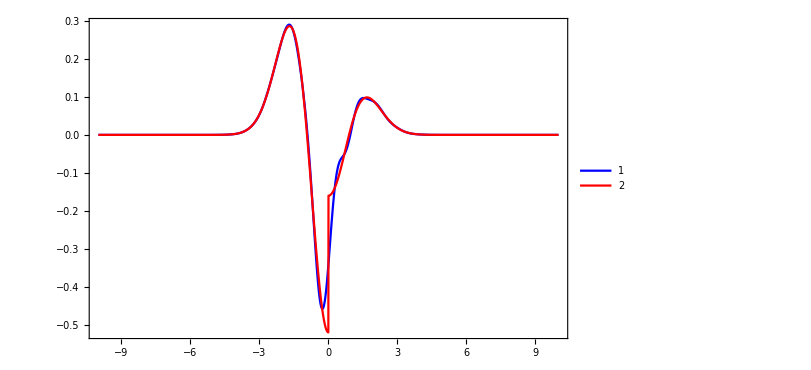

```mathematica
Plot[{(*f[5][c],f[6][c],f[7][c],f[8][c],f[9][c],f[10][c],f[11][c],*)f[50][c],exactf[c]},{c,-10,10},PlotRange->Full,PlotStyle->colorlist⟦1;;9⟧,PlotLegends->Automatic]
```

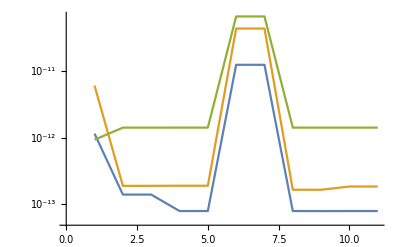

```mathematica
exactρ=Integrate[exactf[c],{c,-∞,∞}];
exactθ=Integrate[(c^2-1)exactf[c],{c,-∞,∞}];
exactv=Integrate[c exactf[c],{c,-∞,∞}];

Numericalρ=Table[NIntegrate[f[ii][c],{c,-10,10}],{ii,5,15}];
Numericalθ=Table[NIntegrate[(c^2-1)f[ii][c],{c,-10,10}],{ii,5,15}];
Numericalv=Table[NIntegrate[c f[ii][c],{c,-10,10}],{ii,5,15}];

errorρ=Abs[exactρ-Numericalρ];
errorv=Abs[exactv-Numericalv];
errorθ=Abs[exactθ-Numericalθ];

ListLogPlot[{errorρ,errorv,errorθ},Joined->True]
```

### Heat Conduction Kn = ∞

#### convergence with points in velocity space

```mathematica
Clear[result2,trialf,spacec,spacex]
```

```mathematica
nx=10;
Kn=∞;
θW0Ref=-1.0;
θW1Ref=1.0;
min=15;
max=80;
diff=5;

initialv=0.0;
initialρ=0.1;
initialθ=θW0Ref;
initialf[c_]:=If[c<0,(c initialv+H[2,c]/(√2)θW1Ref+initialρ)f0[c],(c initialv H[2,c]/(√2)θW0Ref+initialρ)f0[c]];

Do[
Print[Style["Grid Points: ",FontColor->Green],ii];
result2[ii]=SolverFaster[nx,ii,Kn,initialf,θW0Ref,θW1Ref];
spacex[ii]=result2[ii]⟦5⟧;
spacec[ii]=result2[ii]⟦3⟧;
weights[ii]=result2[ii]⟦4⟧;
,{ii,min,max,diff}];
(*errorθ[25]={1/nx,Max[Abs[result2⟦1⟧-exactθ]]};*)
```

Grid Points: 15

Wall at the left

Wall at the right

Performing assemblation

Time Stepping

Velocity at left wall and right wall: 4.16334×10^-17 1.38778×10^-17

Residum: 1.26259×10^-8

Grid Points: 20

Wall at the left

Wall at the right

Performing assemblation

Time Stepping

Velocity at left wall and right wall: 4.16334×10^-17 1.38778×10^-17

Residum: 1.44331×10^-8

Grid Points: 25

Wall at the left

Wall at the right

Performing assemblation

Time Stepping

Velocity at left wall and right wall: 3.46945×10^-17 6.93889×10^-18

Residum: 5.31197×10^-8

Grid Points: 30

Wall at the left

Wall at the right

Performing assemblation

Time Stepping

Velocity at left wall and right wall: 4.85723×10^-17 1.38778×10^-17

Residum: 2.65075×10^-8

Grid Points: 35

Wall at the left

Wall at the right

Performing assemblation

Time Stepping

Velocity at left wall and right wall: 2.77556×10^-17 4.16334×10^-17

Residum: 2.61847×10^-8

Grid Points: 40

Wall at the left

Wall at the right

Performing assemblation

Time Stepping

Velocity at left wall and right wall: 1.38778×10^-17 4.16334×10^-17

Residum: 0.0000160589

Grid Points: 45

Wall at the left

Wall at the right

Performing assemblation

Time Stepping

Velocity at left wall and right wall: 1.38778×10^-17 1.38778×10^-17

Residum: 8.15381×10^-6

Grid Points: 50

Wall at the left

Wall at the right

Performing assemblation

Time Stepping

Velocity at left wall and right wall: 2.77556×10^-17 1.38778×10^-17

Residum: 4.47452×10^-6

Grid Points: 55

Wall at the left

Wall at the right

Performing assemblation

Time Stepping

Velocity at left wall and right wall: 4.16334×10^-17 1.38778×10^-17

Residum: 2.62524×10^-6

Grid Points: 60

Wall at the left

Wall at the right

Performing assemblation

Time Stepping

Velocity at left wall and right wall: 1.38778×10^-17 0.

Residum: 1.73683×10^-6

Grid Points: 65

Wall at the left

Wall at the right

Performing assemblation

Time Stepping

Velocity at left wall and right wall: 6.93889×10^-17 6.93889×10^-18

Residum: 1.27401×10^-6

Grid Points: 70

Wall at the left

Wall at the right

Performing assemblation

Time Stepping

Velocity at left wall and right wall: 6.93889×10^-18 4.16334×10^-17

Residum: 1.02094×10^-6

Grid Points: 75

Wall at the left

Wall at the right

Performing assemblation

Time Stepping

Velocity at left wall and right wall: 5.55112×10^-17 3.46945×10^-17

Residum: 8.94377×10^-7

Grid Points: 80

Wall at the left

Wall at the right

Performing assemblation

Time Stepping

Velocity at left wall and right wall: 1.38778×10^-17 1.38778×10^-17

Residum: 8.13286×10^-7

```mathematica
Clear[f,ρW]
```

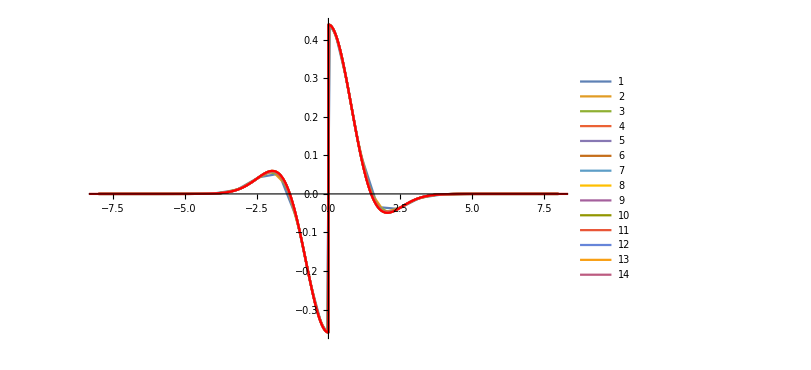

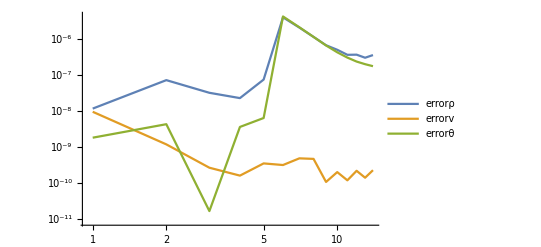

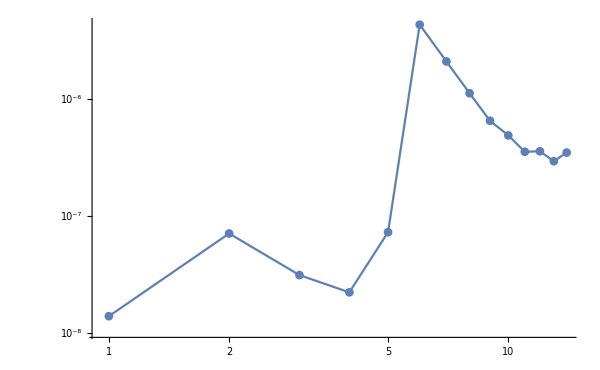

```mathematica
(*phase density function at the first space point but all of velocity points*)
f=Table[Table[{spacec[ii]⟦jj⟧,result2[ii]⟦2⟧⟦jj⟧},{jj,1,Length[spacec[ii]]}],{ii,min,max,diff}];

(*velocity at the wall*)
vLeft=Table[ArrayvPlus[spacec[ii],weights[ii]].f⟦ii/5-2⟧⟦All,2⟧+ArrayvNegative[spacec[ii],weights[ii]].f⟦ii/5-2⟧⟦All,2⟧,{ii,min,max,diff}];

vRight=Table[ArrayvPlus[spacec[ii],weights[ii]].f⟦ii/5-2⟧⟦All,2⟧+ArrayvNegative[spacec[ii],weights[ii]].f⟦ii/5-2⟧⟦All,2⟧,{ii,min,max,diff}];

(*Density at the leftWall*)
ρWLeft=Table[ArrayρW[spacec[ii],weights[ii]].f⟦ii/5-2⟧⟦All,2⟧-θW0Ref/2,{ii,min,max,diff}];
ρWRight=Table[ArrayρWMinus[spacec[ii],weights[ii]].f⟦ii/5-2⟧⟦All,2⟧-θW1Ref/2,{ii,min,max,diff}];


(*ρNegExact is the density of the negative part of the distribution function*)
{ρNegExact,ρPosExact}=ComputeρKn∞[0.1,θW1Ref,θW0Ref];
exactf[c_]:=If[c>0,fM[θW0Ref,0,ρPosExact,c],fM[θW1Ref,0,ρNegExact,c]];

exactρ=Integrate[exactf[c],{c,-∞,∞}];
exactv=Integrate[c exactf[c],{c,-∞,∞}];
exactθ=Integrate[(c^2-1)exactf[c],{c,-∞,∞}];
exactMassFlux={Integrate[c exactf[c],{c,-∞,0}],Integrate[c exactf[c],{c,0,∞}]};

Numericalρ=Table[Arrayρ[spacec[ii],weights[ii]].f⟦ii/5-2⟧⟦All,2⟧,{ii,min,max,diff}];
Numericalv=Table[Arrayv[spacec[ii],weights[ii]].f⟦ii/5-2⟧⟦All,2⟧,{ii,min,max,diff}];
Numericalθ=Table[Arrayθ[spacec[ii],weights[ii]].f⟦ii/5-2⟧⟦All,2⟧,{ii,min,max,diff}];

errorρ=Abs[Numericalρ-exactρ];
errorv=Abs[Numericalv-exactv];
errorθ=Abs[Numericalθ-exactθ];

errorf=Table[Table[{spacec[ii]⟦jj⟧,Abs[(exactf[x]/.{x->spacec[ii]⟦jj⟧})-f⟦ii/5-2⟧⟦All,2⟧⟦jj⟧]},{jj,1,Length[spacec[ii]]}],{ii,min,max,diff}];

L1errorf=Table[weights[ii].errorf⟦ii/5-2⟧⟦All,2⟧,{ii,min,max,diff}];

Show[{ListPlot[f,Joined->True,PlotRange->{Full,Full},PlotLegends->Automatic],Plot[exactf[c],{c,-10,10},PlotRange->{Full,Full}]},ImageSize->600]

ListLogLogPlot[{errorρ,errorv,errorθ},Joined->True,PlotLegends->{"errorρ","errorv","errorθ"}]
ListLogLogPlot[L1errorf,Joined->True,PlotMarkers->Automatic]
```

```mathematica
(*write the values*)
filename="Kninf/f";
Do[Writef[N[spacex[ii]],N[spacec[ii]],N[weights[ii]],Chop[N[result2[ii]⟦2⟧],10^-5],filename];,{ii,min,max,diff}];
```

### Homogeneous relaxation to equilibrium

```mathematica
Clear[result];
θ1=1.0;
ρ1=1.0;

θ2=2.0;
ρ2=3.0;
min=25;
max = 60;
diff = 5;

initialf[c_]:=If[c<0,fM[θ1,0,ρ1,c],fM[θ2,0,ρ2,c]];
exactρ=Integrate[initialf[c],{c,-∞,∞}];
exactv=Integrate[c initialf[c],{c,-∞,∞}];
exactθ=Integrate[(c^2-1)initialf[c],{c,-∞,∞}];
exactf[c_]:=fM[exactθ,exactv,exactρ,c];

Do[result[ii]=HomogeneousSolver[1.0,initialf,ii,0.1];
Numericalρ=Arrayρ[result[ii]⟦2⟧,result[ii]⟦3⟧].result[ii]⟦1⟧;
Numericalv=Arrayv[result[ii]⟦2⟧,result[ii]⟦3⟧].result[ii]⟦1⟧;
Numericalθ=Arrayθ[result[ii]⟦2⟧,result[ii]⟦3⟧].result[ii]⟦1⟧;

errorρ[ii]=Abs[Numericalρ-exactρ];
errorv[ii]=Abs[Numericalv-exactv];
errorθ[ii]=Abs[Numericalθ-exactθ];,{ii,min,max,diff}];
```

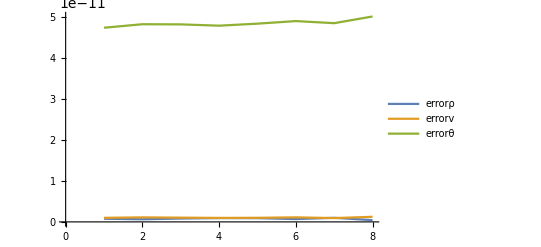

```mathematica
ListPlot[{Table[errorρ[ii],{ii,min,max,diff}],Table[errorv[ii],{ii,min,max,diff}],Table[errorθ[ii],{ii,min,max,diff}]},Joined->True,PlotLegends->{"errorρ","errorv","errorθ"}]
```

### Heat Conduction finite Kn

#### convergence with velocity space(Kn = 0.1)

```mathematica
Clear[result];
nx=25;
Kn=0.1;
θW0Ref=-1.0;
θW1Ref=1.0;
min=25;
max=100;
diff=5;

initialv=0.0;
initialρ=0.1;
initialθ=θW0Ref;
initialf[c_]:=fM[initialθ,initialv,initialρ,c];

Do[
Print[Style["Grid Points: ",FontColor->Green],ii];
result[ii]=SolverFaster[nx,ii,Kn,initialf,θW0Ref,θW1Ref];
spacex[ii]=result[ii]⟦5⟧;
spacec[ii]=result[ii]⟦3⟧;
weights[ii]=result[ii]⟦4⟧;
,{ii,min,max,diff}];
```

Grid Points: 25

Wall at the left

Wall at the right

Performing assemblation

Time Stepping

Velocity at left wall and right wall: 1.11022×10^-16 8.32667×10^-17

Residum: 1.36792×10^-8

Grid Points: 30

Wall at the left

Wall at the right

Performing assemblation

Time Stepping

Velocity at left wall and right wall: 5.55112×10^-17 0.

Residum: 1.21112×10^-8

Grid Points: 35

Wall at the left

Wall at the right

Performing assemblation

Time Stepping

Velocity at left wall and right wall: 2.77556×10^-17 0.

Residum: 1.07431×10^-8

Grid Points: 40

Wall at the left

Wall at the right

Performing assemblation

Time Stepping

Velocity at left wall and right wall: 5.55112×10^-17 5.55112×10^-17

Residum: 1.44223×10^-8

Grid Points: 45

Wall at the left

Wall at the right

Performing assemblation

Time Stepping

Velocity at left wall and right wall: 5.55112×10^-17 2.77556×10^-17

Residum: 3.21248×10^-8

Grid Points: 50

Wall at the left

Wall at the right

Performing assemblation

Time Stepping

Velocity at left wall and right wall: 2.77556×10^-17 5.55112×10^-17

Residum: 4.3642×10^-8

Grid Points: 55

Wall at the left

Wall at the right

Performing assemblation

Time Stepping

Velocity at left wall and right wall: 5.55112×10^-17 2.77556×10^-17

Residum: 4.01489×10^-8

Grid Points: 60

Wall at the left

Wall at the right

Performing assemblation

Time Stepping

Velocity at left wall and right wall: 5.55112×10^-17 8.32667×10^-17

Residum: 5.32351×10^-8

Grid Points: 65

Wall at the left

Wall at the right

Performing assemblation

Time Stepping

Velocity at left wall and right wall: 0. 2.77556×10^-17

Residum: 8.07709×10^-8

Grid Points: 70

Wall at the left

Wall at the right

Performing assemblation

Time Stepping

Velocity at left wall and right wall: 2.77556×10^-17 1.38778×10^-17

Residum: 8.38659×10^-8

Grid Points: 75

Wall at the left

Wall at the right

Performing assemblation

Time Stepping

Velocity at left wall and right wall: 2.77556×10^-17 5.55112×10^-17

Residum: 8.82231×10^-8

Grid Points: 80

Wall at the left

Wall at the right

Performing assemblation

Time Stepping

Velocity at left wall and right wall: 2.77556×10^-17 4.16334×10^-17

Residum: 1.16166×10^-7

Grid Points: 85

Wall at the left

Wall at the right

Performing assemblation

Time Stepping

Velocity at left wall and right wall: 5.55112×10^-17 2.77556×10^-17

Residum: 1.3789×10^-7

Grid Points: 90

Wall at the left

Wall at the right

Performing assemblation

Time Stepping

Velocity at left wall and right wall: 1.11022×10^-16 4.16334×10^-17

Residum: 1.47366×10^-7

Grid Points: 95

Wall at the left

Wall at the right

Performing assemblation

Time Stepping

Velocity at left wall and right wall: 0. 1.38778×10^-17

Residum: 1.80243×10^-7

Grid Points: 100

Wall at the left

Wall at the right

Performing assemblation

Time Stepping

Velocity at left wall and right wall: 8.32667×10^-17 1.38778×10^-17

Residum: 2.08731×10^-7

```mathematica
fLeft=Table[Table[{spacec[ii]⟦jj⟧,result[ii]⟦2⟧⟦jj⟧},{jj,1,Length[spacec[ii]]}],{ii,min,max,diff}];
fRight=Table[Table[{spacec[ii]⟦jj⟧,result[ii]⟦2⟧⟦-Length[spacec[ii]]+jj-1⟧},{jj,1,Length[spacec[ii]]}],{ii,min,max,diff}];
Numericalρ=Table[Arrayρ[spacec[ii],weights[ii]].fLeft⟦ii/5-4⟧⟦All,2⟧,{ii,min,max,diff}];
Numericalv=Table[Arrayv[spacec[ii],weights[ii]].fLeft⟦ii/5-4⟧⟦All,2⟧,{ii,min,max,diff}];
Numericalθ=Table[Table[{spacex[ii]⟦jj⟧-0.5,Arrayθ[spacec[ii],weights[ii]].result[ii]⟦2⟧⟦Length[spacec[ii]]*(jj-1)+1;;Length[spacec[ii]]*jj⟧},{jj,1,Length[spacex[ii]]}],{ii,min,max,diff}];

Interpolationθ=Table[Interpolation[Numericalθ⟦ii⟧],{ii,1,Length[Numericalθ]}];

errorθ=Table[{ii,NIntegrate[Abs[Interpolationθ⟦ii/5-4⟧[x]-Interpolationθ⟦-1⟧[x]],{x,-0.5,0.5}]},{ii,min,max,diff}];
```

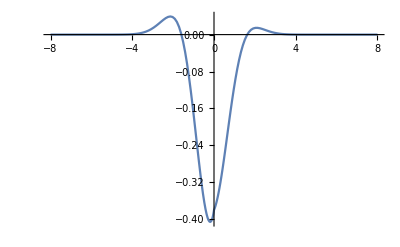

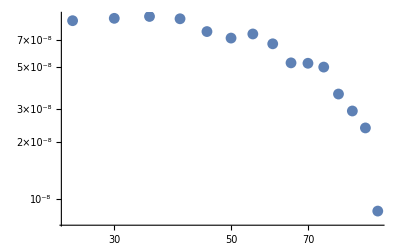

```mathematica
ListPlot[fRight⟦-1⟧,Joined->True]
ListLogLogPlot[errorθ]
```

```mathematica
filename="Kn0p1/f";
Do[Writef[N[spacex[ii]],N[spacec[ii]],N[weights[ii]],Chop[N[result[ii]⟦2⟧],10^-5],filename];,{ii,min,max,diff}];
```

#### convergence with velocity space(Kn = 1.0)

```mathematica
Clear[result];
nx=25;
Kn=1.0;
θW0Ref=-1.0;
θW1Ref=1.0;
min=25;
max=100;
diff=5;

initialv=0.0;
initialρ=0.1;
initialθ=θW0Ref;
initialf[c_]:=fM[initialθ,initialv,initialρ,c];

Do[
Print[Style["Grid Points: ",FontColor->Green],ii];
result[ii]=SolverFaster[nx,ii,Kn,initialf,θW0Ref,θW1Ref];
spacex[ii]=result[ii]⟦5⟧;
spacec[ii]=result[ii]⟦3⟧;
weights[ii]=result[ii]⟦4⟧;
,{ii,min,max,diff}];
```

Grid Points: 25

Wall at the left

Wall at the right

Performing assemblation

Time Stepping

Velocity at left wall and right wall: 4.16334×10^-17 6.93889×10^-17

Residum: 6.73837×10^-10

Grid Points: 30

Wall at the left

Wall at the right

Performing assemblation

Time Stepping

Velocity at left wall and right wall: 2.77556×10^-17 2.08167×10^-17

Residum: 7.87088×10^-10

Grid Points: 35

Wall at the left

Wall at the right

Performing assemblation

Time Stepping

Velocity at left wall and right wall: 2.77556×10^-17 2.77556×10^-17

Residum: 1.13942×10^-9

Grid Points: 40

Wall at the left

Wall at the right

Performing assemblation

Time Stepping

Velocity at left wall and right wall: 6.93889×10^-17 0.

Residum: 1.34464×10^-9

Grid Points: 45

Wall at the left

Wall at the right

Performing assemblation

Time Stepping

Velocity at left wall and right wall: 1.38778×10^-17 6.93889×10^-18

Residum: 1.57686×10^-9

Grid Points: 50

Wall at the left

Wall at the right

Performing assemblation

Time Stepping

Velocity at left wall and right wall: 2.77556×10^-17 3.46945×10^-17

Residum: 2.3797×10^-9

Grid Points: 55

Wall at the left

Wall at the right

Performing assemblation

Time Stepping

Velocity at left wall and right wall: 1.38778×10^-17 2.42861×10^-17

Residum: 3.04033×10^-9

Grid Points: 60

Wall at the left

Wall at the right

Performing assemblation

Time Stepping

Velocity at left wall and right wall: 5.55112×10^-17 2.08167×10^-17

Residum: 3.37369×10^-9

Grid Points: 65

Wall at the left

Wall at the right

Performing assemblation

Time Stepping

Velocity at left wall and right wall: 2.77556×10^-17 6.245×10^-17

Residum: 3.82079×10^-9

Grid Points: 70

Wall at the left

Wall at the right

Performing assemblation

Time Stepping

Velocity at left wall and right wall: 5.55112×10^-17 6.93889×10^-18

Residum: 5.73205×10^-9

Grid Points: 75

Wall at the left

Wall at the right

Performing assemblation

Time Stepping

Velocity at left wall and right wall: 2.77556×10^-17 5.20417×10^-17

Residum: 6.09567×10^-9

Grid Points: 80

Wall at the left

Wall at the right

Performing assemblation

Time Stepping

Velocity at left wall and right wall: 6.93889×10^-17 6.93889×10^-18

Residum: 6.79776×10^-9

Grid Points: 85

Wall at the left

Wall at the right

Performing assemblation

Time Stepping

Velocity at left wall and right wall: 5.55112×10^-17 2.08167×10^-17

Residum: 8.73339×10^-9

Grid Points: 90

Wall at the left

Wall at the right

Performing assemblation

Time Stepping

Velocity at left wall and right wall: 1.38778×10^-17 6.245×10^-17

Residum: 1.00625×10^-8

Grid Points: 95

Wall at the left

Wall at the right

Performing assemblation

Time Stepping

Velocity at left wall and right wall: 2.77556×10^-17 9.02056×10^-17

Residum: 1.04347×10^-8

Grid Points: 100

Wall at the left

Wall at the right

Performing assemblation

Time Stepping

Velocity at left wall and right wall: 4.16334×10^-17 2.77556×10^-17

Residum: 1.15168×10^-8

```mathematica
fLeft=Table[Table[{spacec[ii]⟦jj⟧,result[ii]⟦2⟧⟦jj⟧},{jj,1,Length[spacec[ii]]}],{ii,min,max,diff}];
fRight=Table[Table[{spacec[ii]⟦jj⟧,result[ii]⟦2⟧⟦-Length[spacec[ii]]+jj-1⟧},{jj,1,Length[spacec[ii]]}],{ii,min,max,diff}];
Numericalρ=Table[Arrayρ[spacec[ii],weights[ii]].fLeft⟦ii/5-4⟧⟦All,2⟧,{ii,min,max,diff}];
Numericalv=Table[Arrayv[spacec[ii],weights[ii]].fLeft⟦ii/5-4⟧⟦All,2⟧,{ii,min,max,diff}];
Numericalθ=Table[Table[{spacex[ii]⟦jj⟧-0.5,Arrayθ[spacec[ii],weights[ii]].result[ii]⟦2⟧⟦Length[spacec[ii]]*(jj-1)+1;;Length[spacec[ii]]*jj⟧},{jj,1,Length[spacex[ii]]}],{ii,min,max,diff}];

Interpolationθ=Table[Interpolation[Numericalθ⟦ii⟧],{ii,1,Length[Numericalθ]}];

errorθ=Table[{ii,NIntegrate[Abs[Interpolationθ⟦ii/5-4⟧[x]-Interpolationθ⟦-1⟧[x]],{x,-0.5,0.5}]},{ii,min,max,diff}];
```

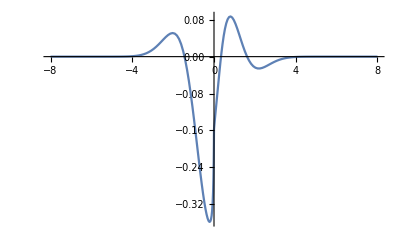

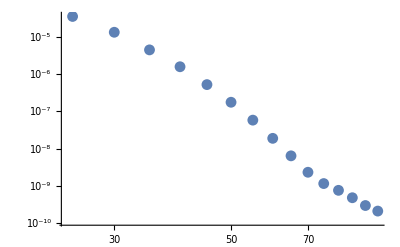

```mathematica
ListPlot[fRight⟦-1⟧,Joined->True,PlotRange->Full]
ListLogLogPlot[errorθ]
```

```mathematica
filename="Kn1p0/f";
Do[Writef[N[spacex[ii]],N[spacec[ii]],N[weights[ii]],Chop[N[result[ii]⟦2⟧],10^-5],filename];,{ii,min,max,diff}];
```

#### convergence with velocity space(Kn = 10.0)

```mathematica
Clear[result];
nx=25;
Kn=10.0;
θW0Ref=-1.0;
θW1Ref=1.0;
min=25;
max=100;
diff=5;

initialv=0.0;
initialρ=0.1;
initialθ=θW0Ref;
initialf[c_]:=fM[initialθ,initialv,initialρ,c];

Do[
Print[Style["Grid Points: ",FontColor->Green],ii];
result[ii]=SolverFaster[nx,ii,Kn,initialf,θW0Ref,θW1Ref];
spacex[ii]=result[ii]⟦5⟧;
spacec[ii]=result[ii]⟦3⟧;
weights[ii]=result[ii]⟦4⟧;
,{ii,min,max,diff}];
```

Grid Points: 25

Wall at the left

Wall at the right

Performing assemblation

Time Stepping

Velocity at left wall and right wall: 3.46945×10^-17 4.51028×10^-17

Residum: 4.0087×10^-8

Grid Points: 30

Wall at the left

Wall at the right

Performing assemblation

Time Stepping

Velocity at left wall and right wall: 3.46945×10^-17 3.46945×10^-18

Residum: 1.10164×10^-8

Grid Points: 35

Wall at the left

Wall at the right

Performing assemblation

Time Stepping

Velocity at left wall and right wall: 2.77556×10^-17 3.1225×10^-17

Residum: 1.27364×10^-8

Grid Points: 40

Wall at the left

Wall at the right

Performing assemblation

Time Stepping

Velocity at left wall and right wall: 8.32667×10^-17 1.38778×10^-17

Residum: 1.43581×10^-8

Grid Points: 45

Wall at the left

Wall at the right

Performing assemblation

Time Stepping

Velocity at left wall and right wall: 6.93889×10^-17 1.73472×10^-17

Residum: 1.4431×10^-8

Grid Points: 50

Wall at the left

Wall at the right

Performing assemblation

Time Stepping

Velocity at left wall and right wall: 2.77556×10^-17 1.73472×10^-17

Residum: 1.63732×10^-8

Grid Points: 55

Wall at the left

Wall at the right

Performing assemblation

Time Stepping

Velocity at left wall and right wall: 6.93889×10^-18 1.38778×10^-17

Residum: 1.76857×10^-8

Grid Points: 60

Wall at the left

Wall at the right

Performing assemblation

Time Stepping

Velocity at left wall and right wall: 5.55112×10^-17 6.93889×10^-18

Residum: 1.96427×10^-8

Grid Points: 65

Wall at the left

Wall at the right

Performing assemblation

Time Stepping

Velocity at left wall and right wall: 2.77556×10^-17 1.04083×10^-17

Residum: 2.10217×10^-8

Grid Points: 70

Wall at the left

Wall at the right

Performing assemblation

Time Stepping

Velocity at left wall and right wall: 2.77556×10^-17 3.1225×10^-17

Residum: 2.43996×10^-8

Grid Points: 75

Wall at the left

Wall at the right

Performing assemblation

Time Stepping

Velocity at left wall and right wall: 2.77556×10^-17 0.

Residum: 2.77499×10^-8

Grid Points: 80

Wall at the left

Wall at the right

Performing assemblation

Time Stepping

Velocity at left wall and right wall: 6.93889×10^-17 1.04083×10^-17

Residum: 2.88199×10^-8

Grid Points: 85

Wall at the left

Wall at the right

Performing assemblation

Time Stepping

Velocity at left wall and right wall: 4.85723×10^-17 1.04083×10^-17

Residum: 2.94318×10^-8

Grid Points: 90

Wall at the left

Wall at the right

Performing assemblation

Time Stepping

Velocity at left wall and right wall: 0. 5.89806×10^-17

Residum: 3.04514×10^-8

Grid Points: 95

Wall at the left

Wall at the right

Performing assemblation

Time Stepping

Velocity at left wall and right wall: 5.55112×10^-17 3.46945×10^-18

Residum: 3.16019×10^-8

Grid Points: 100

Wall at the left

Wall at the right

Performing assemblation

Time Stepping

Velocity at left wall and right wall: 4.16334×10^-17 1.73472×10^-17

Residum: 3.29881×10^-8

```mathematica
fLeft=Table[Table[{spacec[ii]⟦jj⟧,result[ii]⟦2⟧⟦jj⟧},{jj,1,Length[spacec[ii]]}],{ii,min,max,diff}];
fRight=Table[Table[{spacec[ii]⟦jj⟧,result[ii]⟦2⟧⟦-Length[spacec[ii]]+jj-1⟧},{jj,1,Length[spacec[ii]]}],{ii,min,max,diff}];
Numericalρ=Table[Arrayρ[spacec[ii],weights[ii]].fLeft⟦ii/5-4⟧⟦All,2⟧,{ii,min,max,diff}];
Numericalv=Table[Arrayv[spacec[ii],weights[ii]].fLeft⟦ii/5-4⟧⟦All,2⟧,{ii,min,max,diff}];
Numericalθ=Table[Table[{spacex[ii]⟦jj⟧-0.5,Arrayθ[spacec[ii],weights[ii]].result[ii]⟦2⟧⟦Length[spacec[ii]]*(jj-1)+1;;Length[spacec[ii]]*jj⟧},{jj,1,Length[spacex[ii]]}],{ii,min,max,diff}];

Interpolationθ=Table[Interpolation[Numericalθ⟦ii⟧],{ii,1,Length[Numericalθ]}];

errorθ=Table[{ii,NIntegrate[Abs[Interpolationθ⟦ii/5-4⟧[x]-Interpolationθ⟦-1⟧[x]],{x,-0.5,0.5}]},{ii,min,max,diff}];
```

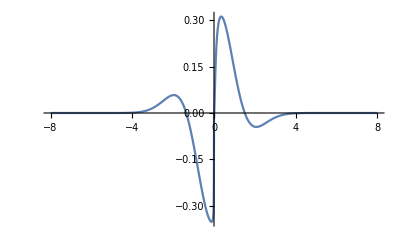

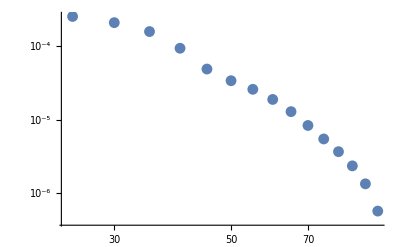

```mathematica
ListPlot[fRight⟦-1⟧,Joined->True,PlotRange->Full]
ListLogLogPlot[errorθ]
```

```mathematica
filename="Kn10p0/f";
Do[Writef[N[spacex[ii]],N[spacec[ii]],N[weights[ii]],Chop[N[result[ii]⟦2⟧],10^-5],filename];,{ii,min,max,diff}];
```

#### convergence with velocity space(Kn = 100.0)

```mathematica
Clear[result];
nx=25;
Kn=100.0;
θW0Ref=-1.0;
θW1Ref=1.0;
min=25;
max=100;
diff=5;

initialv=0.0;
initialρ=0.1;
initialθ=θW0Ref;
initialf[c_]:=fM[initialθ,initialv,initialρ,c];

Do[
Print[Style["Grid Points: ",FontColor->Green],ii];
result[ii]=SolverFaster[nx,ii,Kn,initialf,θW0Ref,θW1Ref];
spacex[ii]=result[ii]⟦5⟧;
spacec[ii]=result[ii]⟦3⟧;
weights[ii]=result[ii]⟦4⟧;
,{ii,min,max,diff}];
```

Grid Points: 25

Wall at the left

Wall at the right

Performing assemblation

Time Stepping

Velocity at left wall and right wall: 3.46945×10^-17 2.08167×10^-17

Residum: 1.01826×10^-8

Grid Points: 30

Wall at the left

Wall at the right

Performing assemblation

Time Stepping

Velocity at left wall and right wall: 5.55112×10^-17 5.55112×10^-17

Residum: 2.92336×10^-7

Grid Points: 35

Wall at the left

Wall at the right

Performing assemblation

Time Stepping

Velocity at left wall and right wall: 3.46945×10^-17 4.16334×10^-17

Residum: 9.8264×10^-8

Grid Points: 40

Wall at the left

Wall at the right

Performing assemblation

Time Stepping

Velocity at left wall and right wall: 5.55112×10^-17 1.38778×10^-17

Residum: 6.47769×10^-8

Grid Points: 45

Wall at the left

Wall at the right

Performing assemblation

Time Stepping

Velocity at left wall and right wall: 4.16334×10^-17 1.38778×10^-17

Residum: 6.77061×10^-8

Grid Points: 50

Wall at the left

Wall at the right

Performing assemblation

Time Stepping

Velocity at left wall and right wall: 0. 3.46945×10^-17

Residum: 2.53942×10^-6

Grid Points: 55

Wall at the left

Wall at the right

Performing assemblation

Time Stepping

Velocity at left wall and right wall: 2.77556×10^-17 4.16334×10^-17

Residum: 6.71672×10^-7

Grid Points: 60

Wall at the left

Wall at the right

Performing assemblation

Time Stepping

Velocity at left wall and right wall: 4.85723×10^-17 4.16334×10^-17

Residum: 2.40199×10^-7

Grid Points: 65

Wall at the left

Wall at the right

Performing assemblation

Time Stepping

Velocity at left wall and right wall: 8.32667×10^-17 0.

Residum: 1.454×10^-7

Grid Points: 70

Wall at the left

Wall at the right

Performing assemblation

Time Stepping

Velocity at left wall and right wall: 8.32667×10^-17 2.77556×10^-17

Residum: 1.238×10^-7

Grid Points: 75

Wall at the left

Wall at the right

Performing assemblation

Time Stepping

Velocity at left wall and right wall: 1.38778×10^-17 6.93889×10^-18

Residum: 1.2454×10^-7

Grid Points: 80

Wall at the left

Wall at the right

Performing assemblation

Time Stepping

Velocity at left wall and right wall: 0. 6.93889×10^-18

Residum: 1.25093×10^-7

Grid Points: 85

Wall at the left

Wall at the right

Performing assemblation

Time Stepping

Velocity at left wall and right wall: 2.77556×10^-17 1.38778×10^-17

Residum: 1.29587×10^-7

Grid Points: 90

Wall at the left

Wall at the right

Performing assemblation

Time Stepping

Velocity at left wall and right wall: 6.245×10^-17 6.93889×10^-18

Residum: 1.32733×10^-7

Grid Points: 95

Wall at the left

Wall at the right

Performing assemblation

Time Stepping

Velocity at left wall and right wall: 2.08167×10^-17 3.46945×10^-17

Residum: 1.33774×10^-7

Grid Points: 100

Wall at the left

Wall at the right

Performing assemblation

Time Stepping

Velocity at left wall and right wall: 2.77556×10^-17 1.38778×10^-17

Residum: 1.32629×10^-7

```mathematica
fLeft=Table[Table[{spacec[ii]⟦jj⟧,result[ii]⟦2⟧⟦jj⟧},{jj,1,Length[spacec[ii]]}],{ii,min,max,diff}];
fRight=Table[Table[{spacec[ii]⟦jj⟧,result[ii]⟦2⟧⟦-Length[spacec[ii]]+jj-1⟧},{jj,1,Length[spacec[ii]]}],{ii,min,max,diff}];
Numericalρ=Table[Arrayρ[spacec[ii],weights[ii]].fLeft⟦ii/5-4⟧⟦All,2⟧,{ii,min,max,diff}];
Numericalv=Table[Arrayv[spacec[ii],weights[ii]].fLeft⟦ii/5-4⟧⟦All,2⟧,{ii,min,max,diff}];
Numericalθ=Table[Table[{spacex[ii]⟦jj⟧-0.5,Arrayθ[spacec[ii],weights[ii]].result[ii]⟦2⟧⟦Length[spacec[ii]]*(jj-1)+1;;Length[spacec[ii]]*jj⟧},{jj,1,Length[spacex[ii]]}],{ii,min,max,diff}];

Interpolationθ=Table[Interpolation[Numericalθ⟦ii⟧],{ii,1,Length[Numericalθ]}];

errorθ=Table[{ii,NIntegrate[Abs[Interpolationθ⟦ii/5-4⟧[x]-Interpolationθ⟦-1⟧[x]],{x,-0.5,0.5}]},{ii,min,max,diff}];
```

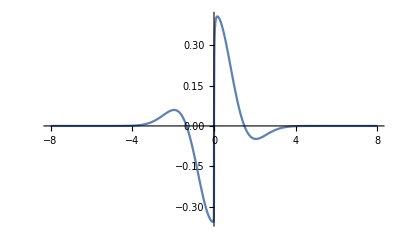

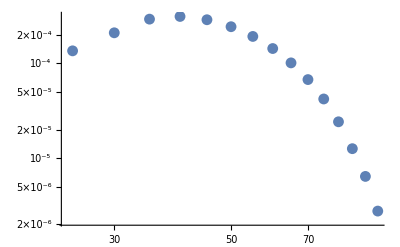

```mathematica
ListPlot[fRight⟦-1⟧,Joined->True,PlotRange->Full]
ListLogLogPlot[errorθ]
```

```mathematica
filename="Kn100p0/f";
Do[Writef[N[spacex[ii]],N[spacec[ii]],N[weights[ii]],Chop[N[result[ii]⟦2⟧],10^-5],filename];,{ii,min,max,diff}];
```

## Rough Work

### convergence of numerical integration

```mathematica
Clear[Numericalf,NumericalIntegralEven,NumericalIntegralOdd]
```

```mathematica
trialf[c_]:=exactf[c];
trialtruevalue = Integrate[trialf[x],{x,-10,10}];

Do[
triallocationx = GaussianQuadratureWeights[ii,-10,10]⟦All,1⟧;
trialW=GaussianQuadratureWeights[ii,-10,10]⟦All,2⟧;

NumericalfEven[ii]=Table[trialf[triallocationx⟦jj⟧],{jj,1,Length[triallocationx]}];

NumericalIntegralEven[ii]=Sum[NumericalfEven[ii]⟦jj⟧trialW⟦jj⟧,{jj,1,Length[trialW]}];

errorEven[ii]={ii,Abs[trialtruevalue-NumericalIntegralEven[ii]]};,{ii,30,50,10}];

Do[
triallocationx = GaussianQuadratureWeights[ii,-10,10]⟦All,1⟧;
trialW=GaussianQuadratureWeights[ii,-10,10]⟦All,2⟧;

NumericalfOdd[ii]=Table[trialf[triallocationx⟦jj⟧],{jj,1,Length[triallocationx]}];

NumericalIntegralOdd[ii]=Sum[NumericalfOdd[ii]⟦jj⟧trialW⟦jj⟧,{jj,1,Length[trialW]}];

errorOdd[ii]={ii,Abs[trialtruevalue-NumericalIntegralOdd[ii]]};,{ii,35,55,10}];
```

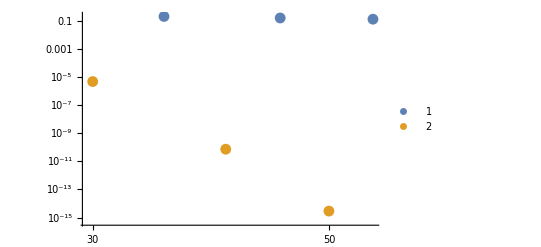

```mathematica
ListLogLogPlot[{Table[errorOdd[ii],{ii,35,55,10}],Table[errorEven[ii],{ii,30,50,10}]},PlotRange->Full,PlotLegends->Automatic]
```

```mathematica
Table[errorOdd[ii],{ii,35,55,10}]
```

{{35,Abs[0.05-If[{-9.97707,-9.87936,-9.70438,-9.45345,-9.12854,-8.73219,-8.2675,-7.7381,-7.14815,-6.50224,-5.80545,-5.06323,-4.28138,-3.46602,-2.62353,-1.76051,-0.883713,0.,0.883713,1.76051,2.62353,3.46602,4.28138,5.06323,5.80545,6.50224,7.14815,7.7381,8.2675,8.73219,9.12854,9.45345,9.70438,9.87936,9.97707}<0,0,fM[θW0,0,0.1,{-9.97707,-9.87936,-9.70438,-9.45345,-9.12854,-8.73219,-8.2675,-7.7381,-7.14815,-6.50224,-5.80545,-5.06323,-4.28138,-3.46602,-2.62353,-1.76051,-0.883713,0.,0.883713,1.76051,2.62353,3.46602,4.28138,5.06323,5.80545,6.50224,7.14815,7.7381,8.2675,8.73219,9.12854,9.45345,9.70438,9.87936,9.97707}]].{0.0588343,0.136508,0.21323,0.288293,0.361101,0.431084,0.497694,0.560408,0.618737,0.672223,0.720448,0.763035,0.799649,0.830006,0.853867,0.871044,0.881405,0.884868,0.881405,0.871044,0.853867,0.830006,0.799649,0.763035,0.720448,0.672223,0.618737,0.560408,0.497694,0.431084,0.361101,0.288293,0.21323,0.136508,0.0588343}]},{45,Abs[0.05-If[{-9.98604,-9.9265,-9.81969,-9.66608,-9.46642,-9.22164,-8.93292,-8.60162,-8.22934,-7.81784,-7.36909,-6.88522,-6.36853,-5.8215,-5.24673,-4.64695,-4.02503,-3.38393,-2.7267,-2.05647,-1.37645,-0.68987,0.,0.68987,1.37645,2.05647,2.7267,3.38393,4.02503,4.64695,5.24673,5.8215,6.36853,6.88522,7.36909,7.81784,8.22934,8.60162,8.93292,9.22164,9.46642,9.66608,9.81969,9.9265,9.98604}<0,0,fM[θW0,0,0.1,{-9.98604,-9.9265,-9.81969,-9.66608,-9.46642,-9.22164,-8.93292,-8.60162,-8.22934,-7.81784,-7.36909,-6.88522,-6.36853,-5.8215,-5.24673,-4.64695,-4.02503,-3.38393,-2.7267,-2.05647,-1.37645,-0.68987,0.,0.68987,1.37645,2.05647,2.7267,3.38393,4.02503,4.64695,5.24673,5.8215,6.36853,6.88522,7.36909,7.81784,8.22934,8.60162,8.93292,9.22164,9.46642,9.66608,9.81969,9.9265,9.98604}]].{0.0358266,0.0832319,0.130311,0.176775,0.222398,0.266962,0.310254,0.352067,0.392202,0.430469,0.466684,0.500675,0.53228,0.561349,0.587742,0.611335,0.632014,0.649682,0.664253,0.67566,0.683846,0.688773,0.690418,0.688773,0.683846,0.67566,0.664253,0.649682,0.632014,0.611335,0.587742,0.561349,0.53228,0.500675,0.466684,0.430469,0.392202,0.352067,0.310254,0.266962,0.222398,0.176775,0.130311,0.0832319,0.0358266}]},{55,Abs[0.05-If[{-9.99061,-9.95058,-9.87869,-9.77516,-9.64031,-9.47459,-9.27851,-9.05272,-8.79792,-8.51495,-8.20469,-7.86816,-7.50642,-7.12063,-6.71204,-6.28195,-5.83173,-5.36283,-4.87675,-4.37505,-3.85934,-3.33126,-2.79252,-2.24482,-1.68994,-1.12964,-0.565728,0.,0.565728,1.12964,1.68994,2.24482,2.79252,3.33126,3.85934,4.37505,4.87675,5.36283,5.83173,6.28195,6.71204,7.12063,7.50642,7.86816,8.20469,8.51495,8.79792,9.05272,9.27851,9.47459,9.64031,9.77516,9.87869,9.95058,9.99061}<0,0,fM[θW0,0,0.1,{-9.99061,-9.95058,-9.87869,-9.77516,-9.64031,-9.47459,-9.27851,-9.05272,-8.79792,-8.51495,-8.20469,-7.86816,-7.50642,-7.12063,-6.71204,-6.28195,-5.83173,-5.36283,-4.87675,-4.37505,-3.85934,-3.33126,-2.79252,-2.24482,-1.68994,-1.12964,-0.565728,0.,0.565728,1.12964,1.68994,2.24482,2.79252,3.33126,3.85934,4.37505,4.87675,5.36283,5.83173,6.28195,6.71204,7.12063,7.50642,7.86816,8.20469,8.51495,8.79792,9.05272,9.27851,9.47459,9.64031,9.77516,9.87869,9.95058,9.99061}]].{0.0240832,0.0559863,0.0877575,0.119252,0.150365,0.180996,0.211048,0.240424,0.26903,0.296774,0.323567,0.349324,0.373962,0.397402,0.419568,0.440391,0.459804,0.477743,0.494152,0.508978,0.522174,0.533697,0.54351,0.551582,0.557888,0.562406,0.565123,0.56603,0.565123,0.562406,0.557888,0.551582,0.54351,0.533697,0.522174,0.508978,0.494152,0.477743,0.459804,0.440391,0.419568,0.397402,0.373962,0.349324,0.323567,0.296774,0.26903,0.240424,0.211048,0.180996,0.150365,0.119252,0.0877575,0.0559863,0.0240832}]}}

```mathematica
GaussianQuadratureWeights[20,-1,1]⟦All,1⟧.GaussianQuadratureWeights[20,-1,1]⟦All,2⟧
```

2.42861×10^-17

```mathematica
NumericalIntegralOdd[35]
```

3.66374×10^-15